```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Quit[]
```

# Workspace Setup

```mathematica
Directory[]
SetDirectory[NotebookDirectory[]]
Directory[]
```

C:\Users\Marcos\Documents

D:\Trabalho-estudos\0-SB\CodigoDoutorado\ScGlioblastom_artigo1

D:\Trabalho-estudos\0-SB\CodigoDoutorado\ScGlioblastom_artigo1

```mathematica
plottingFunctions={Plot,ListPlot,ListLinePlot,ParametricPlot,PolarPlot,LogPlot,LogLinearPlot,LogLogPlot,BarChart,PieChart,Histogram,Plot3D,ListPlot3D,ParametricPlot3D,ListSurfacePlot3D,ListContourPlot3D,ContourPlot3D,BarChart3D,Histogram3D,BoxWhiskerChart , StreamPlot, ContourPlot};
SetOptions[#,{LabelStyle->Directive[Bold,FontFamily->"Times",12],TicksStyle->Directive[FontFamily->"Times",10]}]&/@plottingFunctions;
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.04,.02}][##]&;
```

# Variáveis “Globais”:

```mathematica
gamatrix=Import[NotebookDirectory[]<>"\\inputs\\act_BT_ALL_seurat.xlsx","Data"];
gbmatrix=Import[NotebookDirectory[]<>"\\inputs\\sup_BT_ALL_seurat.xlsx","Data"];

names=gamatrix[[1,1,1;;]]
ngenes=Length[names];

postotal =First[Position[names,#]][[1]]&/@{"CD44","EGFR","IDH1","NEFL"};  (* {"CD44","EGFR","IDH1","IDH2","PGK1","OLIG2","NFIB","STAT3","SP3"}  *)
combinations = Subsets[postotal,{2}]

confidenceLevelDefaultValue=0.95;
(*confidenceLevelDefaultValue=0.68;*)

(* Uso a, sa, b e sb simbolicos. Evitar usar como nome de variáveis *)

SeedRandom[1234];
```

{CD44,CHI3L1,CREB1,E2F1,E2F2,EGFR,EGR1,ETS1,FOXM1,HIF1A,IDH1,IDH2,KLF4,L1CAM,MDM2,MGMT,NANOG,NEFL,NFIB,OLIG2,PAX2,PAX5,PAX8,PGK1,PTEN,RUNX2,SALL4,SMAD3,SOX17,SOX2,SOX4,SOX9,SP1,SP3,STAT3,TERT,TP53,TWIST1,VDR,YY1}

{{1,6},{1,11},{1,18},{6,11},{6,18},{11,18}}

# -Definindo funções para a análise:

## Código para importar dados, clusterizar e obter centroides:

```mathematica
importData[fileName_: "datapoints_seurat_BT_ALL"]:=Module[
{datapoints0, datapoints1,datapoints,fileDirectory},
fileDirectory="\\inputs\\";
datapoints0 =Import[NotebookDirectory[]<>fileDirectory<>fileName<>".xlsx","Data"];
datapoints1 = datapoints0[[1,2;;]] ;
datapoints =Select[datapoints1,UnequalTo[Table[0.,ngenes]]]/. {0.->0};
Return[datapoints];
];

computeClustersNbC[datapoints_, distanceFunction_, postotal_]:=Module[{dataclustnumber, fourtuple, components, dataclust},
dataclustnumber=FindClusters[datapoints[[;;,postotal]],PerformanceGoal->"Quality",CriterionFunction->"StandardDeviation",DistanceFunction->distanceFunction,Method->"NeighborhoodContraction"];        
fourtuple=datapoints[[;;,postotal]];         
components=Table[Position[dataclustnumber,fourtuple[[i]]][[1,1]],{i,Length[datapoints]}];
dataclust=Map[First,GatherBy[Transpose[{datapoints,components}],Last],{2}];
Return[dataclust];
];

computeClustersKmeans[datapoints_, datanclusters_, distanceFunction_, postotal_]:=Module[{components,dataclust},
components=ClusteringComponents[datapoints[[;;,postotal]],datanclusters,1,PerformanceGoal->"Quality",CriterionFunction->"StandardDeviation",DistanceFunction->distanceFunction,Method->"KMeans"];
dataclust=Map[First,GatherBy[Transpose[{datapoints,components}],Last],{2}];
Return[dataclust];
];

(*Function to perform common calculations*)
commonCalculations[dataclust_]:=Module[{databasinsmode,databasinscenters,databasinssigmas,dataweights,dataweightsperc},
databasinsmode=Table[Commonest[dataclust[[n]],1],{n,1,Length[dataclust]}];
databasinscenters=Table[Mean[dataclust[[n]]],{n,1,Length[dataclust]}];
databasinssigmas=Table[StandardDeviation[dataclust[[n]]],{n,1,Length[dataclust]}]+1/100;
dataweights=Table[Length[dataclust[[n]]],{n,1,Length[dataclust]}];
dataweightsperc=dataweights/Total[dataweights];
{databasinsmode,databasinscenters,databasinssigmas,dataweights,dataweightsperc}]
```

## Código para reordenar clusters:

```mathematica
(* findClustersLetters foi a última que fiz desta parte  *)

findClustersLetters[simClusteredData_,methodNBCdataclustTotal_,postotal_]:=Module[{debug,orderedSimCluster,totalNumberOfClusters,nonNullOrderedClusters,filledClustersLetters},
debug=False;
orderedSimCluster=orderedDataCluster[simClusteredData,methodNBCdataclustTotal,postotal];
totalNumberOfClusters = Length[orderedSimCluster];
nonNullOrderedClusters=positionsAndFilledClusters[Map[Dimensions,orderedSimCluster]];
If[debug,Print[nonNullOrderedClusters]];
filledClustersLetters=letters[totalNumberOfClusters][[nonNullOrderedClusters[[;;,1]]]];
filledClustersLetters
];

(*------------------------------------    Funções auxiliares  ---------------------------------------*)

distanceFunc[x_,y_]:=Module[{diff},diff=x-y;Sqrt[Total[diff^2]]]

mahalanobisDistance[x_,y_]:=Module[
{diff,invCov,covMatrix},
diff=x-y;
covMatrix=Covariance[x,y];
invCov=Inverse[covMatrix];
Sqrt[diff.invCov.diff]]

computeCentroids[clusters_List]:=Map[Mean,clusters]

orderingBy[lista_,ref_,func_]:=Ordering[N[Map[func[#,ref]&,lista]]] (* não uso *)

distBy[lista_,ref_,func_]:=N[Map[func[#,ref]&,lista]]

listWithMinValue[lista_]:=Module[{minIndex},minIndex=First[Ordering[lista[[All,1]],1]];lista[[minIndex]]];

fillMissedValues[ lista_, refNclusters_] :=Module[{testCentroidIndices, extraCentroids,orderedIndices},
testCentroidIndices=Range[Length[lista]];
extraCentroids=Complement[testCentroidIndices,Flatten[lista]];
orderedIndices = Join[lista,Select[extraCentroids,#<=refNclusters&]];
Return[orderedIndices]
];

(*-------------------------------------------------------------------------------------------------------------------------*)

mapDistances[refCentroids_List,simCentroids_List]:=Module[
{debug,distList,mappedList,numberOfRefCentroids,numberOfTestCentroids,
listaAgregada,tamanhoListaAgregada,armazenaIndReordenados,salvaIndices,salvaDists,
testandoSorting,indiceDe,indicePara,indiceDist},
debug=False;
numberOfRefCentroids=Length[refCentroids];
numberOfTestCentroids=Length[simCentroids];
distList=distBy[simCentroids,#,distanceFunc]&/@refCentroids;
If[debug,Print[distList]];
mappedList=Flatten[Table[MinimalBy[MapThread[{#1,i,#2}&,{distList[[i]],Range[Length[simCentroids]]}],First],{i,numberOfRefCentroids}],1];
If[debug,Print[mappedList]];
listaAgregada=GatherBy[mappedList,Last];
tamanhoListaAgregada=Length[listaAgregada];
armazenaIndReordenados=Table[{},numberOfRefCentroids];
salvaIndices={};
salvaDists=Table[{},numberOfRefCentroids];
Do[testandoSorting=listWithMinValue[listaAgregada[[i]]];
indiceDe=testandoSorting[[3]];
indicePara=testandoSorting[[2]];
indiceDist=testandoSorting[[1]];
If[MemberQ[indiceDe,salvaIndices],If[indiceDist<salvaDists[[indicePara]],armazenaIndReordenados[[indicePara]]=indiceDe;
salvaDists[[indicePara]]=indiceDist;,armazenaIndReordenados[[indicePara]]=armazenaIndReordenados[[indicePara]]],AppendTo[salvaIndices,indiceDe];
armazenaIndReordenados[[indicePara]]=indiceDe;
salvaDists[[indicePara]]=indiceDist;];,{i,tamanhoListaAgregada}];
armazenaIndReordenados=fillMissedValues[armazenaIndReordenados,numberOfTestCentroids];
Return[armazenaIndReordenados];]

(*------------------------------------Função para mapear distâncias a pares de centróides---------------------------------------*)

reorderAndInsertNew[listaOriginal_,novaOrdem_,novoElemento_]:=Module[{novaLista},
novaLista=Table[If[novaOrdem[[i]]==={},novoElemento,listaOriginal[[novaOrdem[[i]]]]],{i,Length[novaOrdem]}];
novaLista]

orderedDataCluster[dadosParaReordenar_,dadosDeReferencia_,dimensoesParaDistancia_]:=
Module[{debug,centroidesDeReferencia,centroidesparaReordenar,numeroDeClustersNaReferencia,numeroDeClustersParaReordenar,orderedIndices,
testCentroidIndices,extraCentroids,
novoElemento,dataclustnew},
debug=False;

centroidesDeReferencia=Map[#[[dimensoesParaDistancia]]&,computeCentroids[dadosDeReferencia]];
centroidesparaReordenar=Map[#[[dimensoesParaDistancia]]&,computeCentroids[dadosParaReordenar]];

numeroDeClustersNaReferencia=Length[dadosDeReferencia];
numeroDeClustersParaReordenar=Length[dadosParaReordenar];

orderedIndices=mapDistances[centroidesDeReferencia,centroidesparaReordenar];

(* tinha comentado, mas parece que precisa mesmo *)
If[numeroDeClustersParaReordenar>numeroDeClustersNaReferencia,
testCentroidIndices=Range[numeroDeClustersParaReordenar];
extraCentroids=Complement[testCentroidIndices,orderedIndices];
orderedIndices=Flatten[AppendTo[orderedIndices,extraCentroids]],orderedIndices=orderedIndices];

If[debug,Print[orderedIndices]];

novoElemento={};
dataclustnew=reorderAndInsertNew[dadosParaReordenar,orderedIndices,novoElemento];

Return[dataclustnew];
];

(*f[opts_Association]:=Module[{x,y},x=Lookup[opts,"x",valorPadraoX];
y=Lookup[opts,"y",1];
x+y]*)
```

## Código para plots correlação, elipsoides etc:

```mathematica
numberToCapitalLetter[n_Integer]:=ToUpperCase[FromCharacterCode[n+ToCharacterCode["A"]-1]]

letters[cnumber_]:=CharacterRange["A",numberToCapitalLetter[cnumber]];

plotScatterData[dataclust_, postotal_]:=Module[{combinations,datacorr,datacorrexp},
combinations = Subsets[postotal,{2}];
datacorr=Table[Table[Table[
{dataclust[[nbasin,dataPoints,combinations[[i,1]]]],dataclust[[nbasin,dataPoints,combinations[[i,2]]]]},
{i,1,Length[combinations]}],{dataPoints,1,Length[dataclust[[nbasin]]]}],{nbasin,1,Length[dataclust]}];
datacorrexp=Table[
Show[ListPlot[Table[datacorr[[nbasins,;;,landnumber]],{nbasins,1,Length[dataclust]}],ImageSize->300,PlotStyle->PointSize[Tiny],PlotMarkers->Automatic,PlotLegends->letters[Length[dataclust]],LabelStyle->Directive["Times",12],AxesLabel->{names[[combinations[[landnumber,1]]]],names[[combinations[[landnumber,2]]]]}]]
,{landnumber,1,Length[combinations]}];
Return[datacorrexp];
];

getCovarianceAndMean[data_]:=Module[{mean=Mean[data],cov=Covariance[data]},{cov,mean}];

plotPointsAndElipsoid[pointsData_,elipsoidData_,indices_,selectConfidenceLevel_, selectLetters_:False,listOfLetters_:All]:=
Module[
{clustersToPlotPoints,dimNames,dimToPlot,covAndMeans,sigmaFactor,lettersToPlot,datacorrexp3D,maxClusters,
df, confidenceLevel, criticalValue},
maxClusters = Max[Length[elipsoidData], Length[pointsData]];
clustersToPlotPoints=maxClusters;(*Length[elipsoidData];*)
dimNames=names[[indices[[1;;3]]]];
dimToPlot=indices[[1;;3]];
covAndMeans=Table[getCovarianceAndMean[elipsoidData[[nCluster,All,dimToPlot]]],{nCluster,Length[elipsoidData]}];

df=Length[dimToPlot];
confidenceLevel=selectConfidenceLevel;
criticalValue=Quantile[ChiSquareDistribution[df],confidenceLevel];
sigmaFactor=criticalValue (*7.815;  2 sigmas*);

lettersToPlot=If[selectLetters,listOfLetters,letters[maxClusters]];
datacorrexp3D=Show[
ListPointPlot3D[Table[pointsData[[nCluster,All,dimToPlot]],{nCluster,clustersToPlotPoints}],
PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01],PointSize[0.015],PointSize[0.015],PointSize[0.01],PointSize[0.01],PointSize[0.018],PointSize[0.018]},
PlotLegends->lettersToPlot,
LabelStyle->Directive["Times",12],AxesLabel->dimNames,Boxed->True,BoxStyle->Directive[FontFamily->"Times",Black,12],LabelStyle->Directive[FontFamily->"Times",Black,12],PlotTheme->"Detailed", (*ImagePadding->50, ImageSize->Scaled[0.6],*)ImageSize->500,PlotRange->{{-0.5,10},{-0.5,10},{-0.5,10}}],
(*Adicionar elipsoides*)
Graphics3D[{Table[{Opacity[0.4],ColorData[97][nCluster],Ellipsoid[covAndMeans[[nCluster,2]],sigmaFactor*covAndMeans[[nCluster,1]]]},{nCluster,Length[elipsoidData]}]}]];
Return[datacorrexp3D];
];
```

## Código para verificar percetual de pontos dentro dos elipsoides (de referência ou outro):

```mathematica
percentOfPointsInsideElipsoids[pointsData_,elipsoidData_,indices_, selectConfidenceLevel_]:=Module[
{debug=False,rank, dimToPlot,covAndMeans,sigmaFactor,numberOfPointsToPlot,pointsWithin2Sigmas,invCov,mean,percentWithin2Sigmas,
df, confidenceLevel, criticalValue},

dimToPlot=If[ToString[indices] == ToString[0], Table[i,{i,ngenes}],indices[[1;;3]]];

(*rule=0:>RandomReal[{0.01, 0.3}];
covAndMeans=Table[getCovarianceAndMean[elipsoidData[[nCluster,All,dimToPlot]]/. rule],{nCluster,Length[elipsoidData]}];*)
covAndMeans=Table[getCovarianceAndMean[elipsoidData[[nCluster,All,dimToPlot]]],{nCluster,Length[elipsoidData]}];

df=Length[dimToPlot];
confidenceLevel=selectConfidenceLevel;
criticalValue=Quantile[ChiSquareDistribution[df],confidenceLevel];
sigmaFactor=criticalValue (*7.815;  2 sigmas*);

If[debug, Print["df: ", df, "; criticalValue: ", criticalValue ]];

numberOfPointsToPlot=Length[elipsoidData];
percentWithin2Sigmas=Table[

rank=MatrixRank[covAndMeans[[nCluster,1]]];
If[debug, Print["Cluster: ", nCluster, "; rank: ", rank ]];

invCov=Inverse[covAndMeans[[nCluster,1]]];
mean=covAndMeans[[nCluster,2]];
If[Length[pointsData[[nCluster]]]!=0,
N[100*Count[pointsData[[nCluster,All,dimToPlot]],point_/;(point-mean).invCov.(point-mean)<= sigmaFactor]/Length[pointsData[[nCluster]]]]
,0],
{nCluster,numberOfPointsToPlot}];
(*100*pointsWithin2Sigmas/(Length/@pointsData);*)

Table["Cluster "<>ToString[letters[numberOfPointsToPlot][[nCluster]]]<>": "<>ToString[percentWithin2Sigmas[[nCluster]]]<>"%",{nCluster,numberOfPointsToPlot}]
];


percentOfUnclusteredPointsInsideElipsoids[pointsData_,elipsoidData_,indices_, selectConfidenceLevel_,percent_:False]:=Module[
{dimToPlot,covAndMeans,sigmaFactor,numberOfPointsToPlot,pointsWithin2Sigmas,invCov,mean,percentWithin2Sigmas,
df, confidenceLevel, criticalValue},

dimToPlot=indices[[1;;3]];
covAndMeans=Table[getCovarianceAndMean[elipsoidData[[nCluster,All,dimToPlot]]],{nCluster,Length[elipsoidData]}];

df=Length[dimToPlot];
confidenceLevel=selectConfidenceLevel;
criticalValue=Quantile[ChiSquareDistribution[df],confidenceLevel];
sigmaFactor=criticalValue (*7.815;  2 sigmas*);

numberOfPointsToPlot=Length[elipsoidData];
percentWithin2Sigmas=Table[
invCov=Inverse[covAndMeans[[nCluster,1]]];
mean=covAndMeans[[nCluster,2]];
If[percent,
{N[100*Count[pointsData[[All,dimToPlot]],point_/;(point-mean).invCov.(point-mean)<= sigmaFactor]/Length[pointsData]],ToString[Count[pointsData[[All,dimToPlot]],point_/;(point-mean).invCov.(point-mean)<= sigmaFactor]]<>"/"<>ToString[Length[pointsData]]},
N[Count[pointsData[[All,dimToPlot]],point_/;(point-mean).invCov.(point-mean)<= sigmaFactor](*/Length[pointsData]*)]
]
,{nCluster,numberOfPointsToPlot}];
(*Table["Cluster "<>letters[[nCluster]]<>": "<>ToString[percentWithin2Sigmas[[nCluster]]],{nCluster,numberOfPointsToPlot}]*)
(*Join[Table[percentWithin2Sigmas[[nCluster]],{nCluster,numberOfPointsToPlot}],{Length[pointsData]}]*)

If[percent,
Table["Cluster "<>ToString[letters[numberOfPointsToPlot][[nCluster]]]<>": "<>ToString[percentWithin2Sigmas[[nCluster]][[1]]]<>"% and: "<>ToString[percentWithin2Sigmas[[nCluster]][[2]]],{nCluster,numberOfPointsToPlot}],
Table[percentWithin2Sigmas[[nCluster]],{nCluster,numberOfPointsToPlot}]
]
];


(*
Map[Print["Valores para "<>#<>"->",percentOfUnclusteredPointsInsideElipsoids[Flatten[ToExpression[#],1],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue,True]]&, listaDeDatasets];
totalForPorb = 2489;
sucesses=Round[2489*0.15];
(*sucesses=15;*)
estProb=0.17;
binomialProbability[n_,k_,p_]:=N[Binomial[n,k] p^k (1-p)^(n-k)];
binomialProbability[totalForPorb,sucesses,estProb];
1-CDF[BinomialDistribution[totalForPorb,estProb],sucesses-1];
Probability[x≥sucesses,x\[Distributed]BinomialDistribution[totalForPorb,estProb]];
Expectation[x,x\[Distributed]BinomialDistribution[totalForPorb,estProb]];
sucess[n_]:=BinomialDistribution[n,estProb];
DiscretePlot[PDF[sucess[totalForPorb],k],{k,0,totalForPorb},PlotRange->All];
Probability[sucesses-4≤x≤sucesses+4,x\[Distributed]sucess[totalForPorb]];
*)
```

## Código para simular clusters gaussianos:

```mathematica
generateSample[means_, std_]:=Table[RandomVariate[NormalDistribution[means[[i]],std[[i]]]],{i,ngenes}];

generateGaussianNoCrossCorrelated[dataBasinsCenters_, dataBasinsSigmas_, dataweights_ , clustered_: False]:=Module[
{debug=False, Simclusters,nSamplesCluster,newSimData},
(*Gerar os clusters com o número de amostras proporcional*)
Simclusters=Table[
nSamplesCluster=10*dataweights[[nClusters]];
Table[generateSample[dataBasinsCenters[[nClusters]],dataBasinsSigmas[[nClusters]]],{nSamplesCluster}],
{nClusters,Length[dataweights]}];

If[debug,Print[Map[Dimensions[#]&,Simclusters]]];

newSimData=Flatten[Simclusters,1];

If[debug,Print[Dimensions[newSimData]]];

If[clustered, Return[Simclusters], Return[newSimData]];
]

(*{covAndMeans//MatrixForm,covAndMeansSampled//MatrixForm}*)
```

## Código para carregar os dados e computar estatísticas:

```mathematica
(*------------------------------------ Definir dataset de referência e reordenar -------------------------------------------*)

sortingReferenceData[referenceDataClusters_]:=Module[{dataClustersCentroids, novosIndices},
dataClustersCentroids = computeCentroids[referenceDataClusters];
novosIndices = Ordering[dataClustersCentroids];
Print[novosIndices];
Return[referenceDataClusters[[novosIndices]]]
];

refereceDataclustTotal=sortingReferenceData[computeClustersNbC[importData[],EuclideanDistance,postotal]]; 

(*-------------------------------------------------------------------------------------------------------------------------*)

loadAllData[distanceFunction_, postotal_]:=Module[{},
(*Para os dados totais*)
methodNBCdataclustTotal=computeClustersNbC[importData[],distanceFunction,postotal];
(* Aqui embaixo eu estou tentando ordenar os dados referência para ficar equivalente com diferentes distanceFunction *)
methodNBCdataclustTotal=orderedDataCluster[methodNBCdataclustTotal,refereceDataclustTotal,postotal];
{methodNBCdatabasinsmodeTotal,methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightsTotal,methodNBCdataweightspercTotal}=commonCalculations[methodNBCdataclustTotal];

(*Paciente datapoints_seurat_BT_S6*)
methodNBCdataclustBTS6=computeClustersNbC[importData["datapoints_seurat_BT_S6"],distanceFunction,postotal];
{methodNBCdatabasinsmodeBTS6,methodNBCdatabasinscentersBTS6,methodNBCdatabasinssigmasBTS6,methodNBCdataweightsBTS6,methodNBCdataweightspercBTS6}=commonCalculations[methodNBCdataclustBTS6];

(*Paciente datapoints_seurat_BT_S4*)
methodNBCdataclustBTS4=computeClustersNbC[importData["datapoints_seurat_BT_S4"],distanceFunction,postotal];
{methodNBCdatabasinsmodeBTS4,methodNBCdatabasinscentersBTS4,methodNBCdatabasinssigmasBTS4,methodNBCdataweightsBTS4,methodNBCdataweightspercBTS4}=commonCalculations[methodNBCdataclustBTS4];

(*Paciente datapoints_seurat_BT_S1*)
methodNBCdataclustBTS1=computeClustersNbC[importData["datapoints_seurat_BT_S1"],distanceFunction,postotal];
{methodNBCdatabasinsmodeBTS1,methodNBCdatabasinscentersBTS1,methodNBCdatabasinssigmasBTS1,methodNBCdataweightsBTS1,methodNBCdataweightspercBTS1}=commonCalculations[methodNBCdataclustBTS1];

(*Paciente datapoints_seurat_BT_S2*)
methodNBCdataclustBTS2=computeClustersNbC[importData["datapoints_seurat_BT_S2"],distanceFunction,postotal];
{methodNBCdatabasinsmodeBTS2,methodNBCdatabasinscentersBTS2,methodNBCdatabasinssigmasBTS2,methodNBCdataweightsBTS2,methodNBCdataweightspercBTS2}=commonCalculations[methodNBCdataclustBTS2];

(*datapoints_seurat _Regular*)
methodNBCdataclustAllRegularCells=computeClustersNbC[importData["datapoints_seurat_Regular"],distanceFunction,postotal];
{methodNBCdatabasinsmodeAllRegularCells,methodNBCdatabasinscentersAllRegularCells,methodNBCdatabasinssigmasAllRegularCells,methodNBCdataweightsAllRegularCells,methodNBCdataweightspercAllRegularCells}=commonCalculations[methodNBCdataclustAllRegularCells];

(*random generated data*)
methodNBCsimRandomGaussclust=computeClustersNbC[generateGaussianNoCrossCorrelated[methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightsTotal],distanceFunction,postotal];
{methodNBCsimRandomGaussbasinsmode,methodNBCsimRandomGaussbasinscenters,methodNBCsimRandomGaussbasinssigmas,methodNBCsimRandomGaussweights,methodNBCsimRandomGaussweightsperc}=commonCalculations[methodNBCsimRandomGaussclust];
];

clustersAndMarkersStatistics[methodNBCdatabasinscentersTotal_,methodNBCdatabasinssigmasTotal_,postotal_]:=Module[
{numberOfClusters,markerGenes,meansAndStds},

numberOfClusters = Length[methodNBCdatabasinscentersTotal];
markerGenes=postotal[[1;;3]];

meansAndStds=Dataset[Flatten[Table[Map[<|"Cluster"-> #[[1]],"Gene"->#[[2]],"Xbar"->#[[3]],"sigma"->#[[4]]|>&,Thread[{Table[letters[numberOfClusters][[nCluster]],3],names[[markerGenes]],methodNBCdatabasinscentersTotal[[nCluster,markerGenes]], methodNBCdatabasinssigmasTotal[[nCluster,markerGenes]]}]],{nCluster,numberOfClusters}]]];

Export["meansAndStds0.xlsx", meansAndStds]
]
```

{7,3,6,2,4,1,5}

```mathematica
(*Map[Dimensions[Flatten[#,1]]&, {methodNBCdataclustBTS1,methodNBCdataclustBTS2,methodNBCdataclustBTS4,methodNBCdataclustBTS6, methodNBCdataclustTotal,methodNBCdataclustAllRegularCells}]*)
(*Map[Dimensions[#]&, {methodNBCdataclustBTS1,methodNBCdataclustBTS2,methodNBCdataclustBTS4,methodNBCdataclustBTS6, methodNBCdataclustTotal,methodNBCdataclustAllRegularCells}]*)
```

## Código para verificar diferença em usar diferentes distâncias:

```mathematica
datasetForVerificationOfDifferences[refereceDataclustTotal_,postotal_]:=Module[
{refff,euccc,manhhh,diiff0,difff1,datasetForDifferences},

refff = computeCentroids[refereceDataclustTotal];

euccc = computeClustersNbC[importData[],EuclideanDistance,postotal];
euccc = orderedDataCluster[euccc ,refereceDataclustTotal,postotal];
euccc = computeCentroids[methodNBCdataclustTotalEuc];

manhhh = computeClustersNbC[importData[],ManhattanDistance,postotal];
manhhh = orderedDataCluster[manhhh ,refereceDataclustTotal,postotal];
manhhh = computeCentroids[manhhh];

diiff0 = refff - euccc;
difff1 = euccc - manhhh;

datasetForDifferences = Table[<|"Cluster"->numberToCapitalLetter[i],"Max"->Max[difff1[[i]]],"|Min|"->Abs[Min[difff1[[i]]]],"|Mean|"->Abs[Mean[difff1[[i]]]]|>, {i,Length[difff1]}];
datasetForDifferences = Dataset[datasetForDifferences];
Export["datasetForDifferences.xlsx",datasetForDifferences];
];

(*datasetForVerificationOfDifferences[refereceDataclustTotal,postotal]*)
```

## Código para selecionar estatística dos clusters e estimar parâmetros:

```mathematica
selectedClustersStatistics[newVariablesFromSelectedCLusters_,selectingClusters_]:=Module[{temporaryList},
temporaryList = newVariablesFromSelectedCLusters;
temporaryList=Map[#[[selectingClusters]]&,temporaryList];
Return[temporaryList]
];

calcMs0Matrix[kState_,state_,numClusters_,numGenes_]:=Table[kState[[i]]*state[[cms,i]],{cms,1,numClusters},{i,1,numGenes}];

calcActivationMatrix[state_,nestValues_,s_, activationMatrix_,numClusters_,numGenes_,onesMatrix_,identityMatrix_]:=Module[{activation},
activation=Table[(state[[cAM,j]]^nestValues/(s^nestValues+state[[cAM,j]]^nestValues+io))*activationMatrix[[i,j]](*+Which[i==23&&j==1,0.9*state[[cAM,i]],i==14&&j==1, 0.76*state[[cAM,i]],True, 0]*),{cAM,1,numClusters},{i,1,numGenes},{j,1,numGenes}] /.{a-> 1, sa-> 1};
activation=Table[activation[[i]].onesMatrix,{i,1,numClusters}] /.{io-> 0};
activation=Table[activation[[ca,i]],{ca,1,numClusters},{i,1,numGenes},{j,1,numGenes}];
Table[activation[[caf]]*identityMatrix,{caf,1,numClusters}]];

calcInhibitionMatrix[state_,nestValues_,s_,inhibitionMatrix_,numClusters_,numGenes_,onesMatrix_,identityMatrix_]:=Module[{inhibition},
inhibition=Table[(s^nestValues/(s^nestValues+state[[cNM,j]]^nestValues+io))*inhibitionMatrix[[i,j]],{cNM,1,numClusters},{i,1,numGenes},{j,1,numGenes}] /.{b-> 1, sb-> 1};
inhibition=Table[inhibition[[i]].onesMatrix,{i,1,numClusters}] /.{io-> 0};
inhibition=Table[inhibition[[cb,i]],{cb,1,numClusters},{i,1,numGenes},{j,1,numGenes}];
Table[inhibition[[cbf]]*identityMatrix,{cbf,1,numClusters}]
];

(*Function to join activation and inhibition matrices horizontally*)
mergeMatricesHorizontally[activationMatrix_,inhibitionMatrix_,numClusters_]:=Table[Join[activationMatrix[[i]],inhibitionMatrix[[i]],2],{i,1,numClusters}];

(*Function to solve the linear programming problem*)
solveLinearProgramming[cVector_,AMatrix_,bVector_,lowerBoundVector_]:=LinearProgramming[cVector,AMatrix,bVector,lowerBoundVector,Reals,Method->"Simplex"];

parametersEstimation[variablesList_, parSinputs_,parNinputs_, parsLimits_] := Module[
{dataclust,databasinscenters,databasinssigmas,dataweights,
minSvalues,maxSfortest, stepSvalues,minNvalues,maxNfortest, stepNvalues,numberOfLoopRepetitions,infLim, supLim,
parlist={},reslist={},restlist={},maxreslist={},parauxlist={},
numGenes,kstate,testdata,numClusters,state, id, ones, amatrix,bmatrix, maResult, mbResult,ms0Result, m00Result,m, ms,
 m0,n0,lb,AT,B,Aall,ball,cVar,solv0Result, drop},

{dataclust,databasinscenters,databasinssigmas,dataweights}=variablesList; 
{minSvalues,maxSfortest, stepSvalues}=parSinputs;
{minNvalues,maxNfortest, stepNvalues}=parNinputs;
{infLim, supLim}=parsLimits;

numberOfLoopRepetitions =Length[Range[minSvalues,maxSfortest,stepSvalues]] * Length[Range[minNvalues,maxNfortest,stepNvalues]];

numGenes = ngenes;
kstate=Table[1,numGenes];
testdata=databasinscenters;
numClusters=Length[testdata];
state = Table[testdata[[i]],{i,1,numClusters}];
id=IdentityMatrix[numGenes];
ones=Table[1,{i,1,numGenes}];

(*Compute amatrix and bmatrix*)
amatrix=Transpose[Round[gamatrix[[1,2;;,1;;]]]]*(a)+Round[gamatrix[[1,2;;,1;;]]]*IdentityMatrix[numGenes]*(sa-a);
bmatrix=Transpose[Round[gbmatrix[[1,2;;,1;;]]]]*(b)+Round[gbmatrix[[1,2;;,1;;]]]*IdentityMatrix[numGenes]*(sb-b);

ms0Result=calcMs0Matrix[kstate,state,numClusters,numGenes];
ms=Join@@ms0Result;

Monitor[indexNumberOfLoopRepetitions=0;Do[Do[

indexNumberOfLoopRepetitions=indexNumberOfLoopRepetitions+1;

(*Calculate maResult,mbResult,m00Result,ms0Result*)
maResult=calcActivationMatrix[state,nest,sest,amatrix,numClusters,numGenes,ones,id];
mbResult=calcInhibitionMatrix[state,nest,sest,bmatrix,numClusters,numGenes,ones,id];

m00Result=mergeMatricesHorizontally[maResult,mbResult,numClusters];
m=Join@@m00Result;
                           
{m0,n0}=Dimensions[m];
lb=Table[{infLim,supLim},{m0+n0}];
AT=Transpose[m];
B=SparseArray[{{i_,i_}->1},{m0,m0}];
Aall=Join[Transpose[Join[B,-AT]],Transpose[Join[B,AT]]];
ball=Join[-ms,ms];
cVar=Join[Table[1,{m0}],Table[0,{n0}]];

(*Solve linear programming problem*)
solv0Result=solveLinearProgramming[cVar,Aall,ball,lb];
(*Drop first (nclusters*ngenes)+1 elements and append results to lists*)
drop=(numClusters*numGenes)+1;

	      parlist=Append[parlist,solv0Result[[drop;;]]];
	      reslist=Append[reslist,Abs[m.solv0Result[[drop;;]]-ms]];
	      restlist=Append[restlist,Total[Abs[m.solv0Result[[drop;;]]-ms]]];
               maxreslist=Append[maxreslist,Max[Abs[m.solv0Result[[drop;;]]-ms]]];
	      parauxlist=Append[parauxlist,{nest,sest}];

 ,{sest,minSvalues,maxSfortest,stepSvalues}],{nest,minNvalues,maxNfortest,stepNvalues}],ProgressIndicator[Dynamic[indexNumberOfLoopRepetitions],{1,numberOfLoopRepetitions}]]; Return[{parlist,reslist,restlist,maxreslist,parauxlist}];

];
```

## Código para rodar simulação e redefinir possíveis funções de ativação:

```mathematica
(*--------------------------------*)

NewActivationFunction[state_,activationMatrix_,numGenes_,nestValues_, s_,firstParEst_]:=
Module[{activation},
activation=Table[
firstParEst[[i]]*(state[[j]]^nestValues/(s^nestValues+state[[j]]^nestValues+io))*activationMatrix[[i,j]]
,{i,1,numGenes},{j,1,numGenes}]/. {a->1,sa->1,io-> 0};
activation];

NewInhibitionFunction[state_,inhibitionMatrix_,numGenes_,nestValues_, s_,firstParEst_]:=
Module[{inhibition},
inhibition=Table[
firstParEst[[i+numGenes]]*(s^nestValues/(s^nestValues+state[[j]]^nestValues+io))*inhibitionMatrix[[i,j]],
{i,1,numGenes},{j,1,numGenes}]/. {b->1,sb->1,io-> 0};
inhibition];

(*--------------------------------*)
runSimulation[auxParSetNumber_,firstParslist_,secondParsList_,parauxlist_,selectedNoiseFactor_,initialCoNditionValues_,maResultIn_, mbResultIn_,exportPlots_:False, simDuration_:50, simStep_:0.1]:=Module[
{ debug = False,numGenes, amatrix,bmatrix,kstate,ms,(*noiseMultiplicativeFactor, pq isso precisa ser global?*)
statelistForStochSim,derStateDynamicsModel,diffElementsForStochModel,itoStochasticProcess,deltaTimeStep,timeForStochSim,
fisrtPars,secondPars,nest,s,noisefactor,maResult,mbResult,m,drivenForce,systemDynamicsDiffEqs,
eqsToStochasticSim,stochsSimulationresults,maxamostra,plots,hist0,hist00,hist000,
stochasticProc,stochRandomFunction,resultado,resultado0,resultado00,exportplot},

If[debug,Print["simDuration: ", simDuration, "; simStep: ", simStep, "; noisefactor: ", selectedNoiseFactor, "; Method: ", "Euler"(*"StochasticRungeKutta"*)]];

fisrtPars = firstParslist[[auxParSetNumber]];
secondPars = secondParsList[[auxParSetNumber]];
nest=parauxlist[[auxParSetNumber,1]];
s=parauxlist[[auxParSetNumber,2]];
noisefactor=selectedNoiseFactor;

(*Calculate maResult,mbResult,m00Result,ms0Result*)
numGenes = ngenes;
state = Table[ToExpression["x"<>ToString[i]<>"[t]"], {i,1,numGenes}];
amatrix=Transpose[Round[gamatrix[[1,2;;,1;;]]]]*(a)+Round[gamatrix[[1,2;;,1;;]]]*IdentityMatrix[numGenes]*(sa-a);
bmatrix=Transpose[Round[gbmatrix[[1,2;;,1;;]]]]*(b)+Round[gbmatrix[[1,2;;,1;;]]]*IdentityMatrix[numGenes]*(sb-b);

maResult=maResultIn[state,amatrix,numGenes,nest,s,fisrtPars];
mbResult=mbResultIn[state,bmatrix,numGenes,nest,s,fisrtPars] ;

kstate=Table[1,numGenes];
ms = Table[kstate[[i]]*state[[i]],{i,1,numGenes}]; (* kpar *)
m   = Join[maResult,mbResult,2];
drivenForce=m.secondPars - ms ;

derStateDynamicsModel=Dt[state,t];
systemDynamicsDiffEqs=derStateDynamicsModel==drivenForce ;
diffElementsForStochModel = Table[ToExpression["ⅆ x"<>ToString[i]<>"[t]"], {i,1,numGenes}];
noiseMultiplicativeFactor =noisefactor;
eqsToStochasticSim=Table[diffElementsForStochModel[[i]]== (systemDynamicsDiffEqs[[2,i]]) ToExpression["ⅆ t"]+ ToExpression["state[[i]]"<>"noiseMultiplicativeFactor ⅆ w"<>ToString[i]<>"[t]"],{i,1,numGenes}]; 

maxamostra=Length[initialCoNditionValues];
plots={};
hist0={};
hist00={};
hist000={};

deltaTimeStep = simStep;
timeForStochSim=simDuration;
statelistForStochSim = Table[ToExpression["x"<>ToString[i]], {i,1,numGenes}];
itoStochasticProcess = Table[ToExpression["w"<>ToString[l]<>"\[Distributed]WienerProcess[]"],{l,numGenes}];

(*DistributeDefinitions[eqsToStochasticSim,state,statelistForStochSim,initialCoNditionValues,t,itoStochasticProcess,maxamostra,timeForStochSim,deltaTimeStep,exportPlots,names];*)

indexNumberOfLoopRepetitions=0;

stochsSimulationresults=Monitor[Table[
indexNumberOfLoopRepetitions=indexNumberOfLoopRepetitions+1;
stochasticProc=ItoProcess[eqsToStochasticSim,state,{statelistForStochSim,initialCoNditionValues[[amostra]]},t,itoStochasticProcess];
stochRandomFunction=RandomFunction[stochasticProc,{0.,timeForStochSim,deltaTimeStep}(*,Method->"StochasticRungeKutta"*)];
resultado=Normal[stochRandomFunction][[1,-1,2]];
resultado0=Normal[stochRandomFunction][[1,(Round[timeForStochSim/2])/deltaTimeStep,2]];
resultado00=Normal[stochRandomFunction][[1,(Round[timeForStochSim/10])/deltaTimeStep,2]];

If[exportPlots,exportplot=Normal[stochRandomFunction][[1,;;,2]]; {resultado,resultado0,resultado00,exportplot},
{resultado,resultado0,resultado00}],

{amostra,1,maxamostra}],
ProgressIndicator[Dynamic[indexNumberOfLoopRepetitions],{1,maxamostra}]];

{hist0,hist00,hist000}=Transpose[stochsSimulationresults[[All, ;;3]]];
If[exportPlots,plots=stochsSimulationresults[[All,4]];Return[{hist0,hist00,hist000,plots}],Return[{hist0,hist00,hist000}]];

]
```

## Código para gerar valores iniciais, visualizar séries temporais e histogramas (correlação e elipsoides já foi definido acima):

```mathematica
(*generatePointsInMultivariateNormalDistribution[mean_,covarianceMatrix_,sampleSize_]:=Module[{L,z,x},
L=CholeskyDecomposition[covarianceMatrix];
Table[z=RandomVariate[NormalDistribution[],Length[mean]];
x=L.z+mean,{sampleSize}]
];*)

generatePointsInMultivariateNormalDistribution[mean_,covarianceMatrix_]:=Module[
{L,z,x},
L=CholeskyDecomposition[covarianceMatrix];
z=RandomVariate[NormalDistribution[],Length[mean]];
x=L.z+mean
];

generateInitialConditionsInElipsoid[elipsoidData_,indices_,sampleSize_,selectConfidenceLevel_]:=Module[
{dimToPlot,covAndMeans,sigmaFactor,covMatrixSelectedCluster,mean,generatedPoints,
df,confidenceLevel,criticalValue,pointGenerator},

dimToPlot=indices[[1;;3]];
covAndMeans=Table[getCovarianceAndMean[elipsoidData[[nCluster,All,dimToPlot]]],{nCluster,Length[elipsoidData]}];
df=Length[dimToPlot];
confidenceLevel=selectConfidenceLevel;
criticalValue=Quantile[ChiSquareDistribution[df],confidenceLevel];
sigmaFactor=criticalValue;

pointGenerator[cov_,mean_]:=Module[{point,valid},
valid=False;
While[!valid,
(*point=Sqrt[Max[cov]]*RandomVariate[NormalDistribution[0,1],Length[mean]]+mean;*)
point=generatePointsInMultivariateNormalDistribution[mean, cov];
valid=(point-mean).Inverse[cov].(point-mean)<=sigmaFactor;
point=Abs[point](*+Abs[Min[point]]*)(* remover valores negativos *);
];
point];

generatedPoints=Table[
Table[
{covMatrixSelectedCluster,mean}=covAndMeans[[nCluster]];
pointGenerator[covMatrixSelectedCluster,mean],
(*Table[pointGenerator[covMatrixSelectedCluster,mean],{sampleSize}],*)
(*generatePointsInMultivariateNormalDistribution[mean, covMatrixSelectedCluster,sampleSize],*)
{nCluster,Length[elipsoidData]}],
{sampleSize}];

(*generatedPoints*) (* para testar *)
Flatten[generatedPoints,1] 
];


(* para testar *)
(*methodNBCdatabasinscentersTotal[[;;,postotal[[1;;3]]]]
Map[Mean[#]&,generateInitialConditionsInElipsoid[methodNBCdataclustTotal, postotal, 5]]*)

(*generateInitialConditionsInElipsoid[methodNBCdataclustTotal, postotal, 5]*)


generateInitialConditions[basinCenters_,sampleInBasinWithNoise_:5, sampledRandomReal_:5, pertubationAmplitude_:1]:=Module[{initialConditions},
initialConditions =Join[
Flatten[Table[Map[#+pertubationAmplitude*RandomVariate[NormalDistribution[0.5,0.1],ngenes]&, basinCenters],sampleInBasinWithNoise],1],
Table[RandomReal[{0,10},ngenes],sampledRandomReal]];
initialConditions
];

plotingTimeSeries[trajectories_, selectingGenes_: ngenes, selectedSample_:All]:=Module[{plots,plotsPartitioned},
plots=Table[Show[ListLinePlot[trajectories[[selectedSample,;;,i]],Filling->None,PlotLabel->names[[i]],PlotRange->Full,ImageSize->200,Frame->True, FrameLabel->{"Time", "Expression"}],FrameTicks->{{tickFunc,Automatic},{tickFunc,Automatic}}],{i,selectingGenes}];
plotsPartitioned=Partition[plots,5(*,4,{1,1},{}*)];
Grid[plotsPartitioned,Frame->None,Spacings->{1,1}]
];

plotingHistograms[datapoints_,histList_, selectingGenes_: ngenes, selectedSample_:All]:=Module[{histogramsList,plots,plotsPartitioned},
histogramsList = Join[{datapoints},histList,1];
plots=Table[Histogram[Map[#[[selectedSample,i]]&,histogramsList],{0,12,0.5},"Probability",PlotLabel->names[[i]]],{i,selectingGenes}];
plotsPartitioned=Partition[plots,5(*,4,{1,1},{}*)];
Grid[plotsPartitioned,Frame->None,Spacings->{1,1}]
];
```

## Código para identificar parâmetros que levam nos elipsoides:

```mathematica
testParametersforClustersCompat[elipsoidReference_,estimatedParsList_,secondParsList_,hyperparametersList_,initialCoNditionValues_,parIndex_, selectedNoiseFactor_:0.001,timeForSimulation_:20,selectConfidenceLevel_,postotal_]:=Module[
{simStep,exportPlots= False,hist0Method,hist00Method,hist000Method},
(*simStep=0.1;*)
simStep=0.05;
(*simStep=0.01;*)
{hist0Method,hist00Method,hist000Method}=runSimulation[parIndex, estimatedParsList, secondParsList, hyperparametersList, selectedNoiseFactor, initialCoNditionValues,  NewActivationFunction,NewInhibitionFunction, exportPlots, timeForSimulation, simStep];
{percentOfUnclusteredPointsInsideElipsoids[hist0Method,elipsoidReference,postotal,selectConfidenceLevel],hist0Method}
];

spanParametersForClustersCompat[elipsoidReference_,estimatedParsList_,secondParsList_,hyperparametersList_,initialCoNditionValues_,mode_:"storingResults", selectedNoiseFactor_:0.001,timeForSimulation_:20,selectConfidenceLevel_,postotal_]:=Module[
{totalParametersCombinations,parIndex,listOfResults,listOfPoints,bothNonZero,dataPoints, debug=False},

If[debug,Print["selectedNoiseFactor :", selectedNoiseFactor];
Print["timeForSimulation :", timeForSimulation];
Print["selectConfidenceLevel :", selectConfidenceLevel];
Print["postotal :", postotal];
];

totalParametersCombinations=Length[estimatedParsList];
listOfResults={};
listOfPoints={};
parameterNumber=0;
Monitor[Do[parameterNumber = parameterNumber+1;
{bothNonZero,dataPoints}  =testParametersforClustersCompat[elipsoidReference,estimatedParsList,secondParsList,hyperparametersList,initialCoNditionValues,parIndex, selectedNoiseFactor,timeForSimulation,selectConfidenceLevel,postotal];
If[mode == "storingResults",
AppendTo[listOfResults,bothNonZero];AppendTo[listOfPoints,dataPoints],
If[Not[MemberQ[Round[bothNonZero],0]], AppendTo[listOfResults,parIndex]];
];
,{parIndex,totalParametersCombinations}],ProgressIndicator[Dynamic[parameterNumber],{1,totalParametersCombinations}]];
{listOfResults,listOfPoints}
];

deleteZeroCases[list_]:=Module[{zeroRemoved},zeroRemoved=DeleteCases[list,_0.,1]]

(* deleteZeroCases[list[[i]]]]>0 aqui o maior que zero seleciona apenas com uma ou mais estabilidade *)

positionsAndFilledClusters[list_]:=Module[{temporaryList={}},
Do[If[
Length[deleteZeroCases[list[[i]]]]>0,AppendTo[temporaryList,{i,list[[i]]}]]
,{i,Length[list]}];
temporaryList
];
```

## Código para ajustar parâmetros em combinações de clusters e ver quais levam em mais de um:

## Versão atual:

```mathematica
trueOrFalseForEachElement[list_, elementsList_]:=Map[MemberQ[list,#]&,elementsList];

filteredCombinations[methodNBCdataclustTotal_, combinationLength_:2,elementsList_:{4,5}]:=Module[{subSets,newSubset,newSubsetWithoutNull},
subSets = Subsets[Range[Length[methodNBCdataclustTotal]],{combinationLength}];
newSubset =Table[If[MemberQ[trueOrFalseForEachElement[subSets[[i]],elementsList],True],subSets[[i]]],{i, Length[subSets]}];
newSubsetWithoutNull=Cases[newSubset,_?ListQ];
newSubsetWithoutNull
]

substituteListValues[listValues_]:=Map[Thread[postotal[[1;;3]]->#]&,listValues]

substituteCOnfidenceExpressionValues[list_,listValues_]:=Table[ReplacePart[list[[i]],listValues[[i]]],{i,Length[list]}]

clustersCombinationsMoreThanTwo[dataClust_,basinCenters_,basinSigmas_,dataWeightPerc_,parSinputs_,parNinputs_,parsLimits_,combinationLength_:2,elementsList_:{4,5},centroidsSampling_:2, uniformSampling_:0, insideConfidence_:False,selectConfidenceLevel_:0.68,pertubationAmplitude_:0,postotal_,tryAllCombinations_:2,noiseFactor_:0.001,timeForSimulation_:20]:=Module[{clustersCombinations,numberOfClusterCombinations,newVariablesForSelectedCLusters,saveCombinationParameterIndicesAndFilledClusters,
minSvalues,maxSfortest, stepSvalues,minNvalues,maxNfortest, stepNvalues,infLim, supLim,parameterCombinationsNumber,
secondParsList,initialCoNditionValues,selectingClusters,selectedClustersStatisticsLists,positionsAndFilled,
estimatedParsList,residualsList,residualsTotalList,residualsMaxList,hyperparametersList,listOfPromissingParameters,
listOfPoints,listForListOfPoints,listForListOfParameters,positionsToStore,
debug,ruido},

debug=False;

Which[tryAllCombinations==1, clustersCombinations=Flatten[Map[filteredCombinations[dataClust, #,elementsList]&,Range[Length[dataClust]]],1],
tryAllCombinations==2,clustersCombinations=filteredCombinations[dataClust,combinationLength,elementsList],
True,clustersCombinations=ToExpression[tryAllCombinations]
];
(*If[tryAllCombinations, 
clustersCombinations=Flatten[Map[filteredCombinations[dataClust, #,elementsList]&,Range[Length[dataClust]]],1],
clustersCombinations=filteredCombinations[dataClust,combinationLength,elementsList]
];*)
numberOfClusterCombinations=Length[clustersCombinations];
Print["Total number of clusters combinations: ", numberOfClusterCombinations];

newVariablesForSelectedCLusters={dataClust,basinCenters,basinSigmas,dataWeightPerc};

saveCombinationParameterIndicesAndFilledClusters={};
listForListOfPoints={};
listForListOfParameters={};

{minSvalues,maxSfortest, stepSvalues}=parSinputs;
{minNvalues,maxNfortest, stepNvalues}=parNinputs;
{infLim, supLim}=parsLimits;

parameterCombinationsNumber = Length[Range[minSvalues,maxSfortest,stepSvalues]] * Length[Range[minNvalues,maxNfortest,stepNvalues]];
secondParsList=Table[Table[1,2*ngenes],parameterCombinationsNumber];

If[Not[insideConfidence],initialCoNditionValues=generateInitialConditions[basinCenters,centroidsSampling,uniformSampling,pertubationAmplitude]];

If[debug,savedInitialCoNditionValues =initialCoNditionValues;Print[savedInitialCoNditionValues]];

combinationCont=0;
Monitor[Do[combinationCont=combinationCont+1;
selectingClusters=clustersCombinations[[i]];
selectedClustersStatisticsLists=selectedClustersStatistics[newVariablesForSelectedCLusters,selectingClusters];
{estimatedParsList,residualsList,residualsTotalList,residualsMaxList,hyperparametersList}=parametersEstimation[selectedClustersStatisticsLists,parSinputs,parNinputs,parsLimits];

If[insideConfidence,
If[debug,Print[Dimensions[selectedClustersStatisticsLists[[1]]]]];
ruido = generateInitialConditionsInElipsoid[selectedClustersStatisticsLists[[1]], postotal, centroidsSampling,selectConfidenceLevel];
If[debug,Print[Dimensions[selectedClustersStatisticsLists[[2]]]]];
initialCoNditionValues=substituteCOnfidenceExpressionValues[Flatten[Table[selectedClustersStatisticsLists[[2]],centroidsSampling],1],substituteListValues[ruido]];
(*initialCoNditionValues=substituteCOnfidenceExpressionValues[generateInitialConditions[basinCenters,centroidsSampling,0],substituteListValues[ruido]];*)
];

{listOfPromissingParameters,listOfPoints}=spanParametersForClustersCompat[dataClust,estimatedParsList,secondParsList,hyperparametersList,initialCoNditionValues,"storingResults",noiseFactor, timeForSimulation,selectConfidenceLevel, postotal];
positionsAndFilled = positionsAndFilledClusters[listOfPromissingParameters]; (*  aqui eu seleciono os parâmetros então não posso passar todos os pontos*)

If[Length[positionsAndFilled]>0,
(*aqui salvo pontos pq a condição foi satisfeita, pontos mapeados pelo counterIndex*)
(*simClusteredDataComb1 = computeClustersNbC[listOfPoints, EuclideanDistance, postotal];
simCentroidsFound=computeCentroids[orderedDataCluster[simClusteredDataComb1,selectedClustersToEstimation1[[1]],postotal]];*)
positionsToStore=positionsAndFilled[[;;,1]];
AppendTo[listForListOfPoints,{selectingClusters,listOfPoints[[positionsToStore]]}];(*depoins vou ter que clusterizar, reordenar e computar centroides*)
(* ------ *)
AppendTo[listForListOfParameters,{selectingClusters,estimatedParsList[[positionsToStore]]}];
(* ------ *)
AppendTo[saveCombinationParameterIndicesAndFilledClusters,{selectingClusters,positionsAndFilled,hyperparametersList[[positionsToStore]],estimatedParsList[[positionsToStore]]}]
];,

{i,numberOfClusterCombinations}];
,ProgressIndicator[Dynamic[combinationCont],{1,numberOfClusterCombinations}]];
{saveCombinationParameterIndicesAndFilledClusters,listForListOfPoints,listForListOfParameters}
];
```

## Código para gerar Dataset dos dados de combinações e estatísticas:

```mathematica
processCombinations[combination_, parsAndCLusters_, hyperparametersList_,activationParameters_]:=Map[<|"Combination"->combination,"ParIndex"->#[[1]],"ClusterFilled"->#[[2]],"n"->#[[3]],"S"->#[[4]],"ActivationParameters"->#[[5]][[1;;ngenes]],"InhibitionParameters"->#[[5]][[ngenes+1;;2*ngenes]]|>&,Join[Join[parsAndCLusters,hyperparametersList,2],Map[{#}&,activationParameters],2]]
generateCombinationsDataset[listOfClutersCombinationsResult_]:=Flatten[Map[processCombinations[#[[1]],#[[2]],#[[3]],#[[4]]]&,listOfClutersCombinationsResult],1]

processedGroupedDataset[rawDataSet_]:=Module[
{debug,keys,values, flattenedKeysOfValues,inListValuesToLetters, letterKeys,flattenedValuesofValues,output},

debug=False;

keys= Keys[rawDataSet];
If[debug,Print["keys: ",keys]];

values=Values[rawDataSet];
If[debug,Print[values]];

flattenedKeysOfValues = Keys[values];
If[debug,Print["flattenedKeysOfValues: ",flattenedKeysOfValues]];

inListValuesToLetters[list_]:=Map[ToString[formatLettersFromList[#]]&,list];
letterKeys=Map[inListValuesToLetters[#]&,flattenedKeysOfValues] ;
If[debug,Print["letterKeys: ",letterKeys]];

flattenedValuesofValues = Values[values];
If[debug,Print["flattenedValuesofValues: ",flattenedValuesofValues]];

output=<|Table[keys[[i]]-><|Thread[letterKeys[[i]]->flattenedValuesofValues[[i]]]|>,{i,Length[keys]}]|>
]

returnClustersCombinationsStatistics[dataSetCombinations_,print_:False]:=Module[
{ifNotZeroTurnOne,newDataSetOfCombinations,joinAndSortCount,newDataSetOfCombinationsCount,
newDataSetOfCombinationsGather,joinAndSortLength,newDataSetOfCombinationsLength,
combinedStatistics},

(*ifNotZeroTurnOne[list_]:=Map[If[#!=0,1,0]&,list]*)
ifNotZeroTurnOne[list_]:=Table[If[list[[i]]!=0,i,0],{i,Length[list]}];
newDataSetOfCombinations = dataSetCombinations[All,{"ClusterFilled"->ifNotZeroTurnOne}];

(*primeiro output*);
joinAndSortCount[list_]:=Counts[Sort[Join[list]]];
newDataSetOfCombinationsCount=newDataSetOfCombinations[GroupBy["ClusterFilled"], joinAndSortCount, "ParIndex"]//Normal;

(*segundo output*);
newDataSetOfCombinationsGather= newDataSetOfCombinations[GroupBy["ClusterFilled"], joinAndSortCount, "Combination"]//Normal;
newDataSetOfCombinationsGather=processedGroupedDataset[newDataSetOfCombinationsGather];

(*terceiro output*);
joinAndSortLength[list_]:=Length[Sort[Join[list]]];
newDataSetOfCombinationsLength=newDataSetOfCombinations[GroupBy["ClusterFilled"], joinAndSortLength, "ParIndex"]//Normal;

(*juntando outputs*);
combinedStatistics = {newDataSetOfCombinationsCount,newDataSetOfCombinationsGather,newDataSetOfCombinationsLength};
If[print,Print[newDataSetOfCombinationsCount,"\n",newDataSetOfCombinationsGather,"\n",newDataSetOfCombinationsLength]];

combinedStatistics
];

allPointsToDataset[listOfClutersCombinationsPoitsResult_]:=Module[
{indexingSamplings,indexingPars,generatePointsDataset},
indexingSamplings[list_]:=Table[names[[j]]->list[[j]],{j,Length[list]}];
indexingPars[list0_,k_,list1_]:=Table[<|"Combination"->list0,"parIndex"->k,"SamplingIndex"->i,indexingSamplings[list1[[i]]]|>,{i,Length[list1]}];
generatePointsDataset[list0_]:=Flatten[Table[indexingPars[list0[[1]],k,list0[[2,k]]],{k,Length[list0[[2]]]}],2];
Flatten[Map[generatePointsDataset[#]&, listOfClutersCombinationsPoitsResult],1]
];

transformedDataset[dataSetPoints_,dataSetCombinationsReference_]:=Module[
{transformarPointsIndices, newDataSet},

transformarPointsIndices[combinationLabel_,parIndexNumber_]:=Module[
{combinationsAndIndices},
combinationsAndIndices =dataSetCombinationsReference[All,{"Combination","ParIndex"}];
combinationsAndIndices[Select[#Combination==combinationLabel&],"ParIndex"][parIndexNumber]
];
newDataSet=dataSetPoints[All,<|#,"parIndex"->transformarPointsIndices[#[["Combination"]],#[["parIndex"]]]|>&];
newDataSet
];
```

## Código para gerar BarChart etc:

```mathematica
formatLettersFromList[list_]:=Module[{str={},tempList},
tempList=DeleteCases[list,_0];
str=Map[numberToCapitalLetter[#]&,tempList];
ToString[str]
];

CreateBarChartsGrid[data_,rotated_:False]:=Module[
{charts,createSingleChart},
createSingleChart[key_,values_]:=BarChart[
Values[values],ChartLabels->If[rotated,Placed[Flatten[Keys[values]],Axis,Rotate[#,45Degree]& ],Flatten[Keys[values]]],FrameStyle->Directive[FontFamily->"Times",FontSize->If[rotated,8,12]],PlotLabel->"Clusters "<>ToString[formatLettersFromList[key]],ChartStyle->"Pastel",LabelingFunction->Above,
ImageSize->Medium,Frame->True,PlotRange->{0,Max[Values[values]+5]}
];
charts=createSingleChart@@@Normal[data];
Grid[Partition[charts,UpTo[3]],Frame->None]
(*GraphicsGrid[Partition[charts,UpTo[3]],Frame->None]*)
];

CreatePairedBarChartsGrid[data1_,data2_, stringList_,reducedLabels_:False,cols_:4]:=Module[
{combinedKeys,fillMissingKeys,filledData1,filledData2,createPairedChart,completeData1,completeData2,
combinedPars,fillMissingParams,keyForChart,dataForChart1,dataForChart2,data,debug,max},

debug=False;

If[debug,Print["data1: ", data1, "\n", "data2: ", data2]];
If[debug,Print["Keys[data1]: ", Keys[data1], "\n", "Keys[data2]: ", Keys[data2]]];

combinedKeys=Union[Keys[data1],Keys[data2]];
combinedPars=Union[Flatten[Keys[Values[data1]]],Flatten[Keys[Values[data2]]]];

If[debug,Print["combinedKeys: ", combinedKeys, "\n", "combinedPars: ", combinedPars]];

fillMissingKeys[data_,keys_]:=Association[Map[If[KeyExistsQ[data,#],#->data[#],#-><||>]&,keys]];
filledData1=fillMissingKeys[data1,combinedKeys];
filledData2=fillMissingKeys[data2,combinedKeys];

If[debug,Print["filledData1: ", filledData1, "\n", "filledData2: ", filledData2]];

fillMissingParams[data_,combinedPars_]:=Module[{updatedData},
updatedData=<||>;
updatedData=Keys[data]->Join@@Table[<|combinedPars[[i]]->If[MemberQ[Flatten[Keys[Values[data]]],combinedPars[[i]]],Lookup[Values[data],combinedPars[[i]]],0]|>,{i, Length[combinedPars]}];
updatedData];

completeData1=AssociationMap[fillMissingParams[#,combinedPars]&,filledData1];
completeData2=AssociationMap[fillMissingParams[#,combinedPars]&,filledData2];

If[debug,Print["completeData1: ", completeData1, "\n", "completeData2: ", completeData2]];

keyForChart=Keys[Values[completeData1]][[1]];

dataForChart1=Values[Values[completeData1]];
dataForChart2=Values[Values[completeData2]];
data = Join[Map[{#}&,dataForChart1], Map[{#}&,dataForChart2],Map[{#}&,combinedKeys],2];

createPairedChart[data_]:=Module[{},

If[debug,Print[data[[1]],"\n",keyForChart]];

max = Max[Flatten[{data[[1]],data[[2]]}]]+2;

PairedBarChart[data[[1]],data[[2]],PlotLabel->"Clusters "<>ToString[formatLettersFromList[data[[3]]]],BarSpacing->{Automatic,0,1}(*{0,0,0.5}*),Method->{"LabelStyle"->"Short"},ColorFunction->"Pastel",PlotRange->{{Automatic,Automatic},{Automatic, Automatic}}(*, ChartStyle->Directive[FontFamily->"Times",FontSize->25]*),LabelingFunction->(Placed[Row[{"","",#1,""},""],Center]&),ImageSize->If[reducedLabels,{300,800},{300,500}(*{{10,400},{320,400}}*)],ImageMargins->1,Frame->True,PlotRange->All,FrameStyle->Directive[FontFamily->"Times",FontSize->16],LabelStyle->Directive[FontFamily->"Times",FontSize->14], AspectRatio->If[reducedLabels,3,1.8],ImagePadding->{{Automatic,Automatic},{Automatic,20}},PlotRangePadding->If[reducedLabels,{{Automatic,Automatic},{Automatic,3}},{{Automatic,Automatic},{Automatic,Automatic}}],FrameTicks->{{None,None},{Range[0,max,Round[max/5]],None}},ChartLabels->{Placed[{stringList[[1]],stringList[[2]]},Above],None,If[reducedLabels,Placed[Map[Style[#,Bold,FontSize->8]&,keyForChart],"LeftAxis"],Placed[keyForChart,"LeftAxis"]]}]
];
Grid[Partition[createPairedChart/@data,UpTo[cols]],Frame->None]
];


plotFinalBarCharts[joinedData_,stringList_, reducedPlots_: True]:=Module[
{max, joinedInputs, plotBasCharts},

max=Max[Flatten[joinedData]+85];

joinedInputs=Table[{joinedData[[i]],stringList[[i]]},{i,Length[stringList]}];

plotBasCharts[valuesInput_,max_]:=Module[{},
BarChart[Values[valuesInput[[1]]],PlotLabel->valuesInput[[2]],ChartLabels->If[reducedPlots,Placed[Map[formatLettersFromList[#]&,Keys[valuesInput[[1]]]],Axis,Rotate[#,45 Degree]&],Keys[valuesInput[[1]]]],FrameStyle->Directive[FontFamily->"Times",FontSize->If[True,8,12]],ChartStyle->"Pastel",BarSpacing->{0.5,Automatic,Automatic},LabelingFunction->Above,Frame->True,ImageSize->All,PlotRange->{0,max},ImageMargins->1,PlotRangePadding->{{0,0},{0,150}},LabelStyle->Directive[FontFamily->"Times",FontSize->8]]]; 

exportFinalGridCounts=Grid[Partition[Map[plotBasCharts[#,max]&,joinedInputs],UpTo[4]],Frame->None];

exportFinalGridCounts
];
```

# Parte 1: Analise visual dos elipsoides para dados single-cell usando diferentes métricas:

## Verificando os percentuais dentro dos elipsoides (EuclideanDistance) - análise com 40 e com 3 genes:

```mathematica
(* Carregando com distância Euclidiana *)
loadAllData[EuclideanDistance, postotal];
```

```mathematica
listaDeDatasets = {"methodNBCdataclustTotal", "methodNBCdataclustBTS1", "methodNBCdataclustBTS2", "methodNBCdataclustBTS4", "methodNBCdataclustBTS6","methodNBCdataclustAllRegularCells"};
Print["\n"]
Map[Print["Número de clusters de "<>#<>" :",Dimensions[ToExpression[#]]]&,listaDeDatasets];
Print["\n"]
Map[Print["Valores para "<>#<>"->",percentOfPointsInsideElipsoids[orderedDataCluster[ToExpression[#],methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]]&, listaDeDatasets];
Print["\n"]
orderedsimUnclustered = orderedDataCluster[methodNBCsimRandomGaussclust,methodNBCdataclustTotal,postotal];
percentOfPointsInsideElipsoids[orderedsimUnclustered,orderedsimUnclustered, postotal,confidenceLevelDefaultValue]
percentOfPointsInsideElipsoids[orderedsimUnclustered,methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsimUnclustered, postotal,confidenceLevelDefaultValue]
```

Número de clusters de methodNBCdataclustTotal :{7}

Número de clusters de methodNBCdataclustBTS1 :{5}

Número de clusters de methodNBCdataclustBTS2 :{8}

Número de clusters de methodNBCdataclustBTS4 :{9}

Número de clusters de methodNBCdataclustBTS6 :{7}

Número de clusters de methodNBCdataclustAllRegularCells :{6}

Valores para methodNBCdataclustTotal->{Cluster A: 84.6154%,Cluster B: 91.954%,Cluster C: 91.7073%,Cluster D: 94.0217%,Cluster E: 92.5795%,Cluster F: 94.1176%,Cluster G: 93.75%}

Valores para methodNBCdataclustBTS1->{Cluster A: 81.5789%,Cluster B: 95.5556%,Cluster C: 99.1803%,Cluster D: 0%,Cluster E: 0%,Cluster F: 0%,Cluster G: 0.%}

Valores para methodNBCdataclustBTS2->{Cluster A: 76.4706%,Cluster B: 80.%,Cluster C: 64.2857%,Cluster D: 97.4576%,Cluster E: 94.5%,Cluster F: 97.1429%,Cluster G: 95.4545%}

Valores para methodNBCdataclustBTS4->{Cluster A: 94.4444%,Cluster B: 75.%,Cluster C: 85.7143%,Cluster D: 80.9524%,Cluster E: 93.4783%,Cluster F: 90.%,Cluster G: 100.%}

Valores para methodNBCdataclustBTS6->{Cluster A: 77.7778%,Cluster B: 100.%,Cluster C: 97.4359%,Cluster D: 100.%,Cluster E: 90.2439%,Cluster F: 100.%,Cluster G: 100.%}

Valores para methodNBCdataclustAllRegularCells->{Cluster A: 95.7198%,Cluster B: 90.625%,Cluster C: 80.1802%,Cluster D: 0%,Cluster E: 0%,Cluster F: 85.1682%,Cluster G: 74.8485%}

{Cluster A: 94.9833%,Cluster B: 95.4965%,Cluster C: 95.8722%,Cluster D: 96.6742%,Cluster E: 95.5872%,Cluster F: 94.7538%,Cluster G: 93.1429%}

{Cluster A: 93.7291%,Cluster B: 92.6097%,Cluster C: 94.2506%,Cluster D: 96.8433%,Cluster E: 93.3808%,Cluster F: 91.5254%,Cluster G: 86.8571%}

{Cluster A: 84.6154%,Cluster B: 91.954%,Cluster C: 92.1951%,Cluster D: 91.8478%,Cluster E: 92.9329%,Cluster F: 94.958%,Cluster G: 96.875%}

## Dados e elipsoides ; 95%, 68% e 20%; 40 genes e 3 genes:

```mathematica
orderedsim=generateGaussianNoCrossCorrelated[methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightsTotal,True];

Print["95%: Gaussian X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, 0,0.95]
Print["95%: Gaussian X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, postotal,0.95]
Print["95%: BT_All X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, 0,0.95]
Print["95%: BT_All X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, postotal,0.95]
Print["95%: BT_All X BT_All (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,methodNBCdataclustTotal, postotal,0.95]

Print["68%: Gaussian X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, 0,0.68]
Print["68%: Gaussian X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, postotal,0.68]
Print["68%: BT_All X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, 0,0.68]
Print["68%: BT_All X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, postotal,0.68]
Print["68%: BT_All X BT_All (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,methodNBCdataclustTotal, postotal,0.68]

Print["20%: Gaussian X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, 0,0.20]
Print["20%: Gaussian X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[orderedsim,orderedsim, postotal,0.20]
Print["20%: BT_All X Gaussian (40 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, 0,0.20]
Print["20%: BT_All X Gaussian (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,orderedsim, postotal,0.20]
Print["20%: BT_All X BT_All (3 genes)"];
percentOfPointsInsideElipsoids[methodNBCdataclustTotal,methodNBCdataclustTotal, postotal,0.20]
```

95%: Gaussian X Gaussian (40 genes)

{Cluster A: 96.1538%,Cluster B: 94.5977%,Cluster C: 95.6585%,Cluster D: 95.2717%,Cluster E: 95.4417%,Cluster F: 95.2101%,Cluster G: 97.5%}

95%: Gaussian X Gaussian (3 genes)

{Cluster A: 94.5299%,Cluster B: 94.8276%,Cluster C: 95.3171%,Cluster D: 95.5435%,Cluster E: 94.841%,Cluster F: 94.7059%,Cluster G: 95.3125%}

95%: BT_All X Gaussian (40 genes)

{Cluster A: 88.8889%,Cluster B: 86.2069%,Cluster C: 87.3171%,Cluster D: 88.0435%,Cluster E: 84.8057%,Cluster F: 87.395%,Cluster G: 96.875%}

95%: BT_All X Gaussian (3 genes)

{Cluster A: 84.6154%,Cluster B: 91.954%,Cluster C: 91.7073%,Cluster D: 93.4783%,Cluster E: 93.2862%,Cluster F: 94.958%,Cluster G: 93.75%}

95%: BT_All X BT_All (3 genes)

{Cluster A: 84.6154%,Cluster B: 91.954%,Cluster C: 91.7073%,Cluster D: 94.0217%,Cluster E: 92.5795%,Cluster F: 94.1176%,Cluster G: 93.75%}

68%: Gaussian X Gaussian (40 genes)

{Cluster A: 67.4359%,Cluster B: 67.931%,Cluster C: 67.8537%,Cluster D: 68.2065%,Cluster E: 67.6678%,Cluster F: 68.6555%,Cluster G: 66.25%}

68%: Gaussian X Gaussian (3 genes)

{Cluster A: 66.8376%,Cluster B: 66.4368%,Cluster C: 68.439%,Cluster D: 67.337%,Cluster E: 67.9859%,Cluster F: 68.0672%,Cluster G: 68.125%}

68%: BT_All X Gaussian (40 genes)

{Cluster A: 85.4701%,Cluster B: 80.4598%,Cluster C: 77.561%,Cluster D: 76.087%,Cluster E: 74.9117%,Cluster F: 78.1513%,Cluster G: 81.25%}

68%: BT_All X Gaussian (3 genes)

{Cluster A: 77.7778%,Cluster B: 81.6092%,Cluster C: 84.3902%,Cluster D: 67.9348%,Cluster E: 75.6184%,Cluster F: 77.3109%,Cluster G: 71.875%}

68%: BT_All X BT_All (3 genes)

{Cluster A: 77.7778%,Cluster B: 78.1609%,Cluster C: 83.4146%,Cluster D: 68.4783%,Cluster E: 75.9717%,Cluster F: 75.6303%,Cluster G: 71.875%}

20%: Gaussian X Gaussian (40 genes)

{Cluster A: 18.8034%,Cluster B: 20.6897%,Cluster C: 19.5122%,Cluster D: 20.5435%,Cluster E: 19.6466%,Cluster F: 20.5042%,Cluster G: 16.875%}

20%: Gaussian X Gaussian (3 genes)

{Cluster A: 22.3077%,Cluster B: 20.1149%,Cluster C: 21.4146%,Cluster D: 19.837%,Cluster E: 20.4594%,Cluster F: 19.8319%,Cluster G: 20.3125%}

20%: BT_All X Gaussian (40 genes)

{Cluster A: 69.2308%,Cluster B: 70.1149%,Cluster C: 62.439%,Cluster D: 57.6087%,Cluster E: 61.1307%,Cluster F: 64.7059%,Cluster G: 50.%}

20%: BT_All X Gaussian (3 genes)

{Cluster A: 70.0855%,Cluster B: 41.3793%,Cluster C: 55.122%,Cluster D: 23.913%,Cluster E: 35.689%,Cluster F: 42.8571%,Cluster G: 25.%}

20%: BT_All X BT_All (3 genes)

{Cluster A: 70.0855%,Cluster B: 34.4828%,Cluster C: 55.122%,Cluster D: 23.3696%,Cluster E: 34.9823%,Cluster F: 40.3361%,Cluster G: 18.75%}

## Analisando os elipsoides (EuclideanDistance)

```mathematica
elipsoidPlotsEuc={
plotPointsAndElipsoid[orderedDataCluster[methodNBCdataclustBTS1,methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue],
plotPointsAndElipsoid[orderedDataCluster[methodNBCdataclustBTS2,methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue],
plotPointsAndElipsoid[orderedDataCluster[methodNBCdataclustBTS4,methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue],
plotPointsAndElipsoid[orderedDataCluster[methodNBCdataclustBTS6,methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue],
plotPointsAndElipsoid[methodNBCdataclustTotal,methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue],
plotPointsAndElipsoid[orderedDataCluster[methodNBCdataclustAllRegularCells,methodNBCdataclustTotal,postotal],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]
};

plotsPartitionedEuc=Partition[elipsoidPlotsEuc,2(*,4,{1,1},{}*)];
plotsPartitionedEucExport=Grid[plotsPartitionedEuc,Frame->None,Spacings->{0,0}]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
(*Do[Export["Euclid"<>StringTake[ToString[confidenceLevelDefaultValue],{3,-1}]<>ToString[i]<>".pdf",elipsoidPlots[[i]]],{i,Length[elipsoidPlots]}]*)
Export["plotsPartitionedEucExport.pdf",plotsPartitionedEucExport]
```

plotsPartitionedEucExport.pdf

```mathematica
orderedsimEucplots={plotPointsAndElipsoid[orderedsim,orderedsim, postotal,confidenceLevelDefaultValue],plotPointsAndElipsoid[orderedsim,methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]};

plotsPartitionedEucOrderedsim=Partition[orderedsimEucplots,2(*,4,{1,1},{}*)];
plotsPartitionedEucOrderedsimExport =Grid[plotsPartitionedEucOrderedsim,Frame->None,Spacings->{0,0}]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export["plotsPartitionedEucOrderedsimExport.pdf",plotsPartitionedEucOrderedsimExport]
```

plotsPartitionedEucOrderedsimExport.pdf

## Verificando os pontos (Unclustered) dentro dos elipsoides (EuclideanDistance):

```mathematica
(* Carregando com distância Euclidiana *)
loadAllData[EuclideanDistance, postotal];

(* Table with mean and standard deviations of each cluster *)
(* clustersAndMarkersStatistics[methodNBCdatabasinscentersTotal, methodNBCdatabasinssigmasTotal, postotal] *)
```

```mathematica
listaDeDatasets = {"methodNBCdataclustTotal", "methodNBCdataclustBTS1", "methodNBCdataclustBTS2", "methodNBCdataclustBTS4", "methodNBCdataclustBTS6","methodNBCdataclustAllRegularCells"};
Print["\n"]
Map[Print["Número de clusters de "<>#<>" :",Dimensions[ToExpression[#]]]&,listaDeDatasets];
Print["\n"]
Map[Print["Valores para "<>#<>"->",percentOfUnclusteredPointsInsideElipsoids[Flatten[ToExpression[#],1],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]]&, listaDeDatasets];
Print["\n"]
orderedsim = orderedDataCluster[methodNBCsimRandomGaussclust,methodNBCdataclustTotal,postotal];
percentOfUnclusteredPointsInsideElipsoids[Flatten[orderedsim,1],orderedsim, postotal,confidenceLevelDefaultValue]
percentOfUnclusteredPointsInsideElipsoids[Flatten[orderedsim,1],methodNBCdataclustTotal, postotal,confidenceLevelDefaultValue]
percentOfUnclusteredPointsInsideElipsoids[Flatten[methodNBCdataclustTotal,1],orderedsim, postotal,confidenceLevelDefaultValue]
```

Número de clusters de methodNBCdataclustTotal :{7}

Número de clusters de methodNBCdataclustBTS1 :{5}

Número de clusters de methodNBCdataclustBTS2 :{8}

Número de clusters de methodNBCdataclustBTS4 :{9}

Número de clusters de methodNBCdataclustBTS6 :{7}

Número de clusters de methodNBCdataclustAllRegularCells :{6}

Valores para methodNBCdataclustTotal->{99.,81.,193.,175.,272.,116.,30.}

Valores para methodNBCdataclustBTS1->{62.,53.,129.,2.,1.,4.,0.}

Valores para methodNBCdataclustBTS2->{13.,8.,20.,146.,190.,75.,21.}

Valores para methodNBCdataclustBTS4->{17.,6.,6.,18.,43.,27.,5.}

Valores para methodNBCdataclustBTS6->{7.,14.,38.,9.,38.,10.,4.}

Valores para methodNBCdataclustAllRegularCells->{1082.,61.,89.,15.,7.,557.,253.}

{114.,85.,197.,176.,269.,121.,30.}

{113.,78.,191.,174.,267.,118.,30.}

{100.,82.,194.,171.,268.,127.,29.}

# Parte 2-testando com timestep 0.05, Euler e SimTime 200: TODAS combinações de clusters Euclidean :

## Rodar análise:

```mathematica
(*-- carregador novamente os dados para garantir --*)
loadAllData[EuclideanDistance, postotal];
(*---------------------------------------------*)
```

```mathematica
(* Nesta configuração default eu já tive bons resultados e rodou rápido, agoura vou investigar refinando *)
parSinputs = {0.5,4, 0.5};
parNinputs = {1,4, 0.5};
parsLimits={1/100, 10};

selectedNoiseFactor = 0.001;
selectedTimeForSimulation = 200;

samplingsToRun = 1;
uniformSampling = 0;
pertubationAmplitude = 0;
combinationsToTest=1;  (*  entra no modo de todas as combinações com 4 e 5*)

AbsoluteTiming[aLLCOMBeuclideanListOfClutersCombinationsResult95 = clustersCombinationsMoreThanTwo[methodNBCdataclustTotal,methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightspercTotal,parSinputs,parNinputs,parsLimits,1,{1,2,3,4,5,6,7},samplingsToRun,uniformSampling,False,0.95,pertubationAmplitude,postotal,combinationsToTest, selectedNoiseFactor,selectedTimeForSimulation];]
Dimensions[aLLCOMBeuclideanListOfClutersCombinationsResult95]
```

Total number of clusters combinations: 127

{22780.7,Null}

{3,127}

```mathematica
AbsoluteTiming[aLLCOMBeuclideanListOfClutersCombinationsResult68 = clustersCombinationsMoreThanTwo[methodNBCdataclustTotal,methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightspercTotal,parSinputs,parNinputs,parsLimits,1,{1,2,3,4,5,6,7},samplingsToRun,uniformSampling,False,0.68,pertubationAmplitude,postotal,combinationsToTest, selectedNoiseFactor,selectedTimeForSimulation];]
Dimensions[aLLCOMBeuclideanListOfClutersCombinationsResult68]
```

Total number of clusters combinations: 127

{23183.7,Null}

{3,127}

## Gerando Dataset:

```mathematica
aLLCOMBdataSetCombinationsEuclidean95=Dataset[generateCombinationsDataset[aLLCOMBeuclideanListOfClutersCombinationsResult95[[1]]]];

aLLCOMBdataSetCombinationsEuclidean68=Dataset[generateCombinationsDataset[aLLCOMBeuclideanListOfClutersCombinationsResult68[[1]]]];
```

## Exportando Dataset:

```mathematica
Export["aLLCOMBdataSetCombinationsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx", aLLCOMBdataSetCombinationsEuclidean95]

Export["aLLCOMBdataSetCombinationsEuclidean68_nSampling_"<>ToString[samplingsToRun]<>".xlsx", aLLCOMBdataSetCombinationsEuclidean68]
```

aLLCOMBdataSetCombinationsEuclidean95_nSampling_1.xlsx

aLLCOMBdataSetCombinationsEuclidean68_nSampling_1.xlsx

## Importando Datasets :

```mathematica
aLLCOMBdataSetCombinationsEuclidean95Imported=Import["aLLCOMBdataSetCombinationsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetCombinationsEuclidean95Imported = aLLCOMBdataSetCombinationsEuclidean95Imported[All,{"Combination"->ToExpression,"ParIndex"->Round, "ClusterFilled"->ToExpression}];

aLLCOMBdataSetCombinationsEuclidean68Imported=Import["aLLCOMBdataSetCombinationsEuclidean68_nSampling_"<>ToString[samplingsToRun]<>".xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetCombinationsEuclidean68Imported = aLLCOMBdataSetCombinationsEuclidean68Imported[All,{"Combination"->ToExpression,"ParIndex"->Round, "ClusterFilled"->ToExpression}];
```

```mathematica
(*aLLCOMBdataSetCombinationsEuclidean95Imported=Import["SimTime200EulerTimestep005-aLLCOMBdataSetCombinationsEuclidean95_nSampling_1.xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetCombinationsEuclidean95Imported = aLLCOMBdataSetCombinationsEuclidean95Imported[All,{"Combination"->ToExpression,"ParIndex"->Round, "ClusterFilled"->ToExpression}];

aLLCOMBdataSetCombinationsEuclidean68Imported=Import["SimTime200EulerTimestep005-aLLCOMBdataSetCombinationsEuclidean68_nSampling_1.xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetCombinationsEuclidean68Imported = aLLCOMBdataSetCombinationsEuclidean68Imported[All,{"Combination"->ToExpression,"ParIndex"->Round, "ClusterFilled"->ToExpression}];*)
```

```mathematica
aLLCOMBdataSetCombinationsEuclidean95= aLLCOMBdataSetCombinationsEuclidean95Imported;

aLLCOMBdataSetCombinationsEuclidean68= aLLCOMBdataSetCombinationsEuclidean68Imported;
```

## Clusters encontrados juntos e com quais frequências:

```mathematica
aLLcombinationsStatisticsEuclidean95= returnClustersCombinationsStatistics[aLLCOMBdataSetCombinationsEuclidean95, False];

aLLcombinationsStatisticsEuclidean68 = returnClustersCombinationsStatistics[aLLCOMBdataSetCombinationsEuclidean68, False];
```

## BarChart:

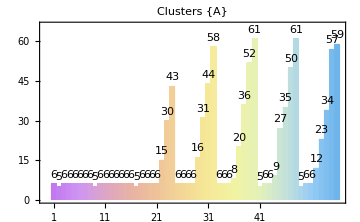
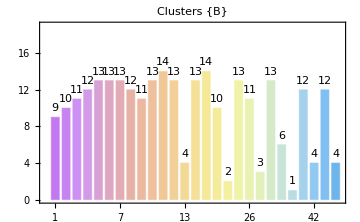
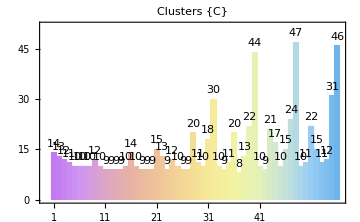
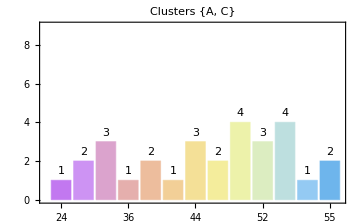
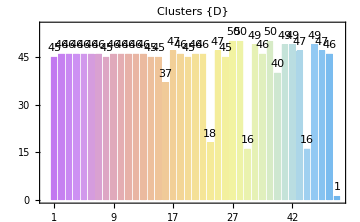
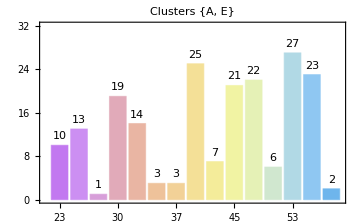
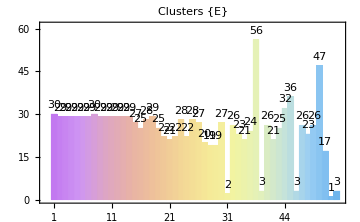
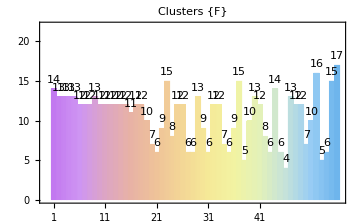
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
index=1;
CreateBarChartsGrid[aLLcombinationsStatisticsEuclidean95[[index]]]
(*Grid[{Map[CreateBarChartsGrid[#]&,{combinationsStatisticsEuclidean95One[[1]],combinationsStatisticsEuclidean68One[[1]],combinationsStatisticsManhattan95One[[1]],combinationsStatisticsManhattan68One[[1]]}]},Frame->False]*)
```

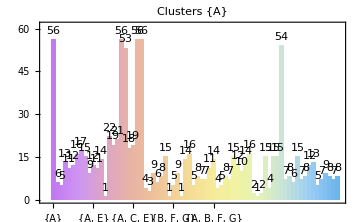
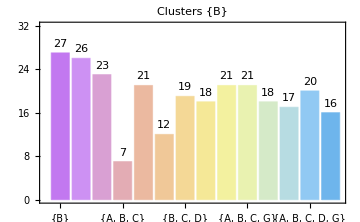
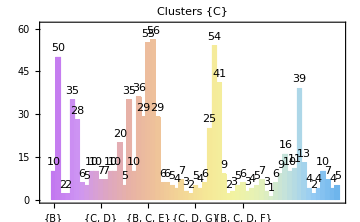
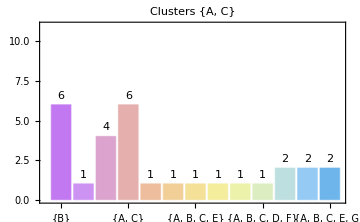
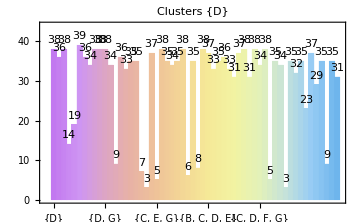
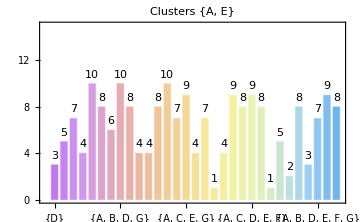
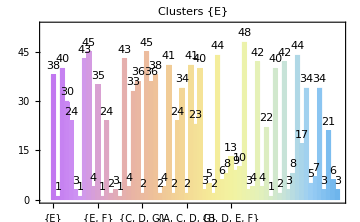
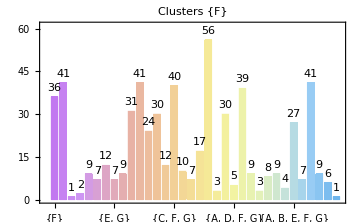
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
index=2;
CreateBarChartsGrid[aLLcombinationsStatisticsEuclidean95[[index]],True]
```

## Grid de barcharts pareados

## Euclidean for parameters:

```mathematica
index=1;
refPairedBarChartData1 = KeySort[aLLcombinationsStatisticsEuclidean68[[index]]];
editedPairedBarChartData1 = aLLcombinationsStatisticsEuclidean95[[index]];
editedPairedBarChartData1 = KeySort[KeyTake[editedPairedBarChartData1,Keys[refPairedBarChartData1]]];

Keys[editedPairedBarChartData1] 
Keys[refPairedBarChartData1]
```

{{0,0,0,0,0,0,7},{0,0,0,0,0,6,0},{0,0,0,0,5,0,0},{0,0,0,0,5,6,0},{0,0,0,4,0,0,0},{0,0,3,0,0,0,0},{0,0,3,0,5,0,0},{0,2,0,0,0,0,0},{0,2,3,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,6,0},{1,0,0,0,5,0,0},{1,0,3,0,0,0,0}}

{{0,0,0,0,0,0,7},{0,0,0,0,0,6,0},{0,0,0,0,5,0,0},{0,0,0,0,5,6,0},{0,0,0,4,0,0,0},{0,0,3,0,0,0,0},{0,0,3,0,5,0,0},{0,2,0,0,0,0,0},{0,2,3,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,6,0},{1,0,0,0,5,0,0},{1,0,3,0,0,0,0}}

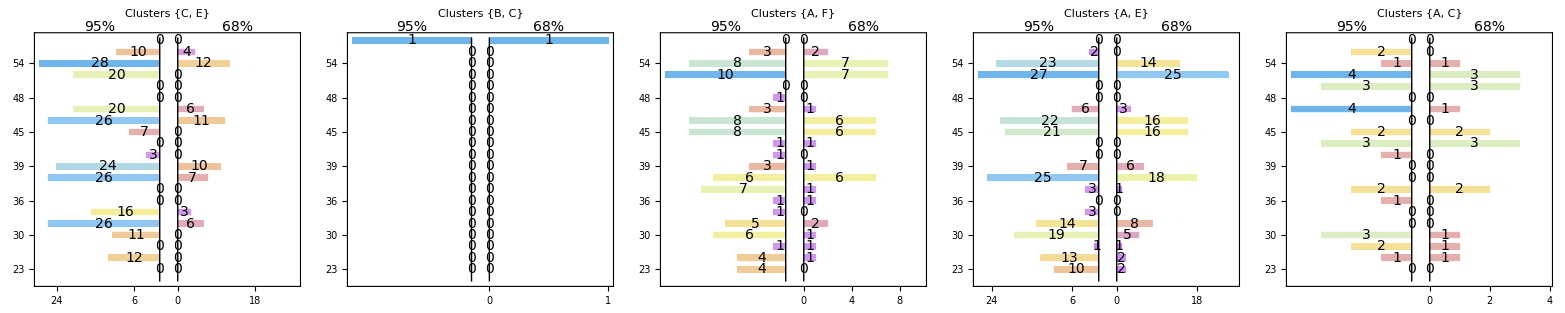

```mathematica
index=1;
listOfPairedBarChart = {7,9,11,12,13};
export1 = CreatePairedBarChartsGrid[editedPairedBarChartData1[[listOfPairedBarChart]],refPairedBarChartData1[[listOfPairedBarChart]],{"95%", "68%"},False,5]
```

```mathematica
Export["paramsAllCombsEuclidean.pdf",export1]
```

paramsAllCombsEuclidean.pdf

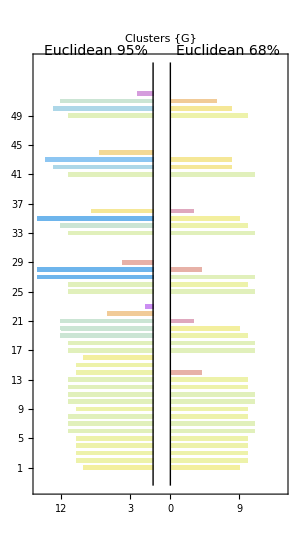
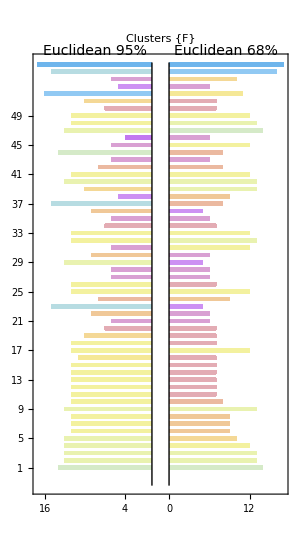
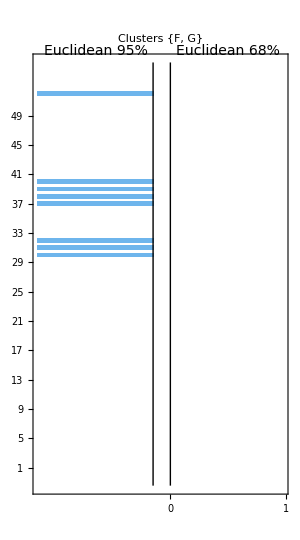
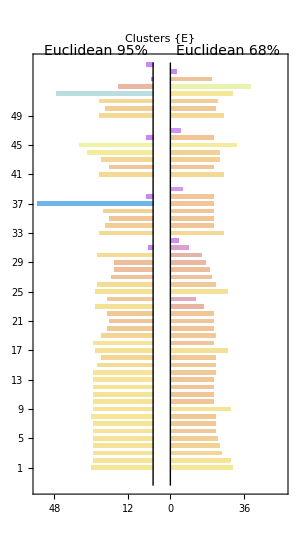
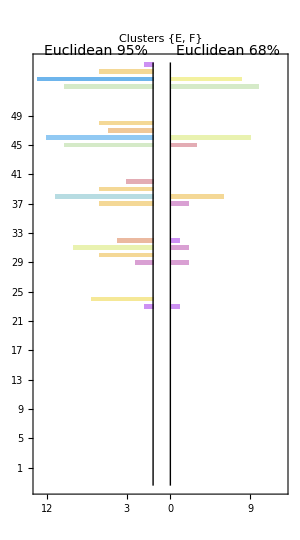
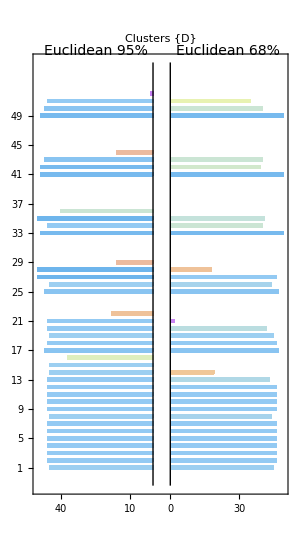
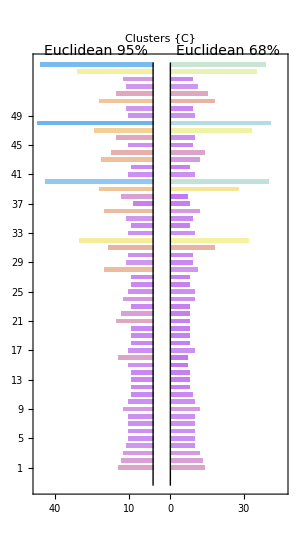
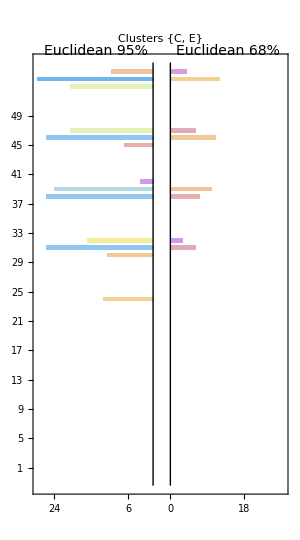
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
index=1;
CreatePairedBarChartsGrid[aLLcombinationsStatisticsEuclidean95[[index]],aLLcombinationsStatisticsEuclidean68[[index]],{"Euclidean 95%", "Euclidean 68%"}]
```

## Euclidean for combinations:

```mathematica
index=2;
refPairedBarChartData2 = KeySort[aLLcombinationsStatisticsEuclidean68[[index]]];
editedPairedBarChartData2 = aLLcombinationsStatisticsEuclidean95[[index]];
editedPairedBarChartData2 = KeySort[KeyTake[editedPairedBarChartData2,Keys[refPairedBarChartData2]]];

Keys[editedPairedBarChartData2] 
Keys[refPairedBarChartData2]
```

{{0,0,0,0,0,0,7},{0,0,0,0,0,6,0},{0,0,0,0,5,0,0},{0,0,0,0,5,6,0},{0,0,0,4,0,0,0},{0,0,3,0,0,0,0},{0,0,3,0,5,0,0},{0,2,0,0,0,0,0},{0,2,3,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,6,0},{1,0,0,0,5,0,0},{1,0,3,0,0,0,0}}

{{0,0,0,0,0,0,7},{0,0,0,0,0,6,0},{0,0,0,0,5,0,0},{0,0,0,0,5,6,0},{0,0,0,4,0,0,0},{0,0,3,0,0,0,0},{0,0,3,0,5,0,0},{0,2,0,0,0,0,0},{0,2,3,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,6,0},{1,0,0,0,5,0,0},{1,0,3,0,0,0,0}}

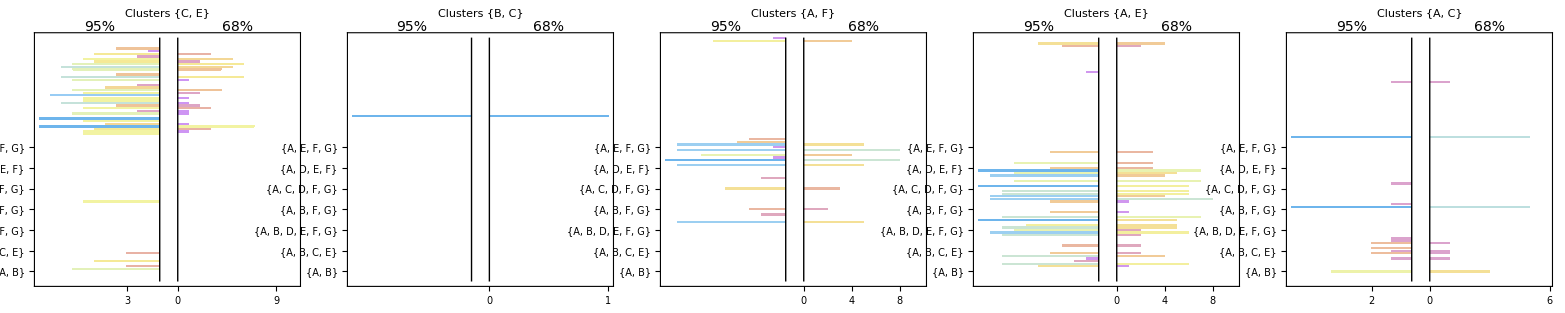

```mathematica
index=2;
listOfPairedBarChart2 = {7,9,11,12,13};
export2 = CreatePairedBarChartsGrid[editedPairedBarChartData2[[listOfPairedBarChart2]],refPairedBarChartData2[[listOfPairedBarChart2]],{"95%", "68%"},True,5]
```

```mathematica
Export["combsAllCombsEuclidean.pdf",export2]
```

combsAllCombsEuclidean.pdf

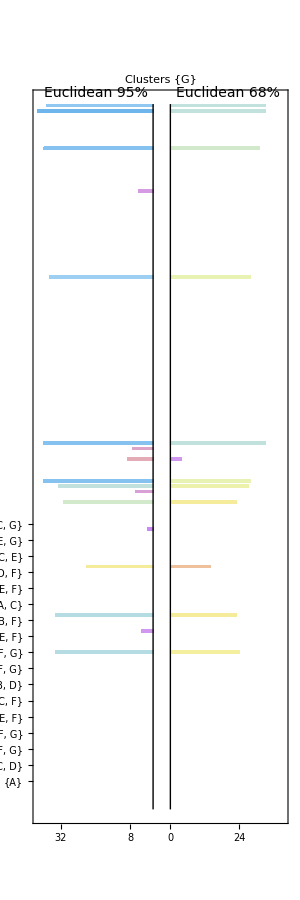
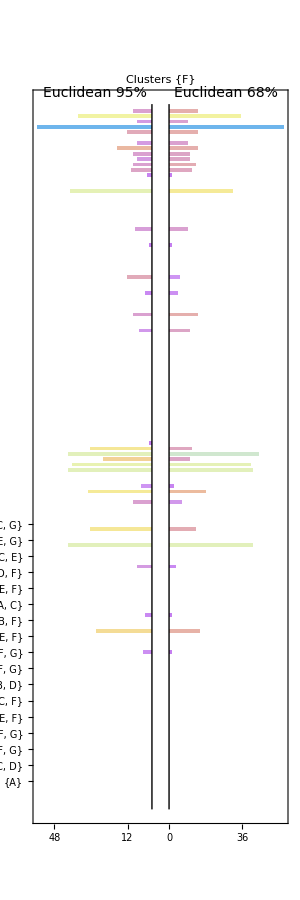
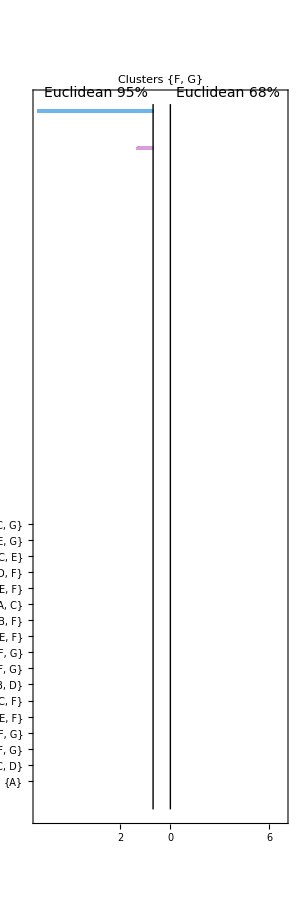
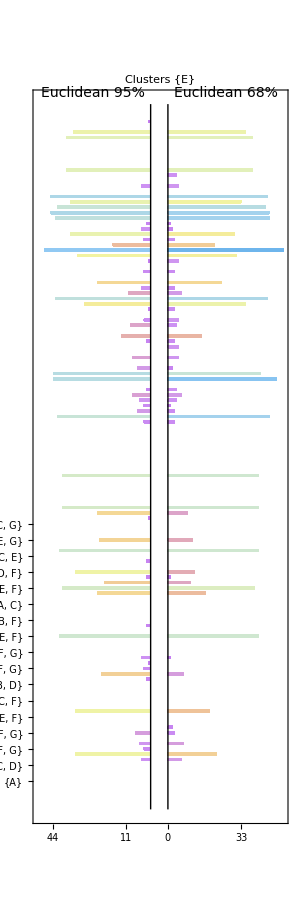
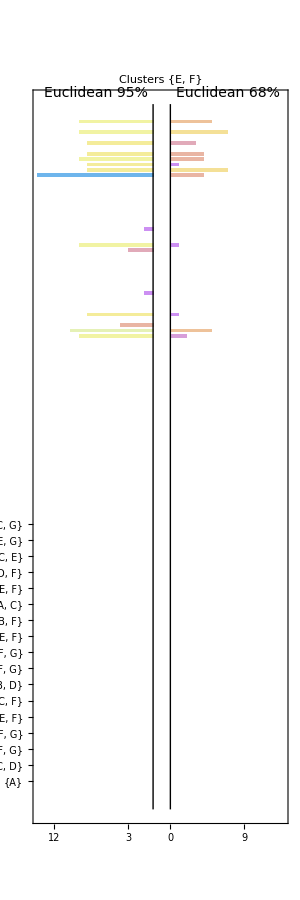
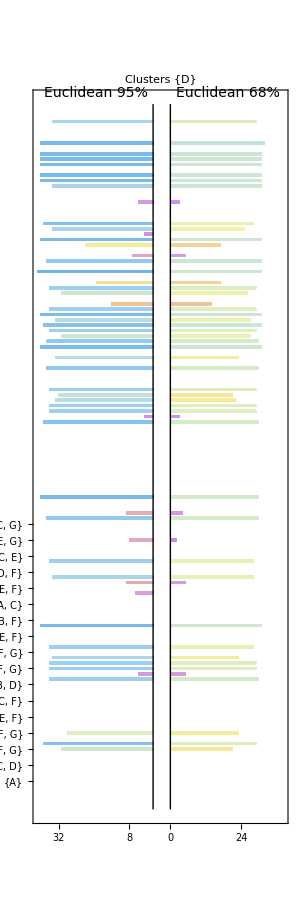
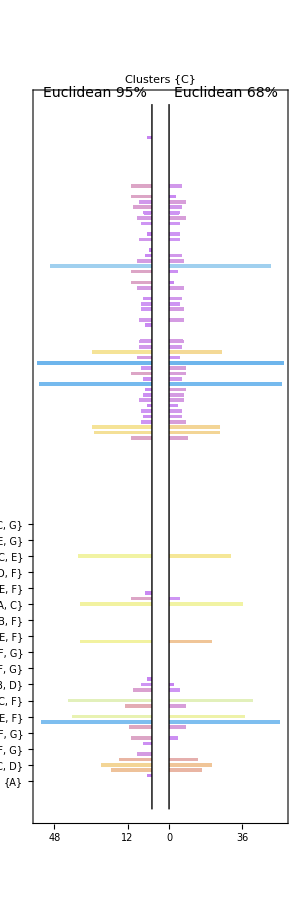
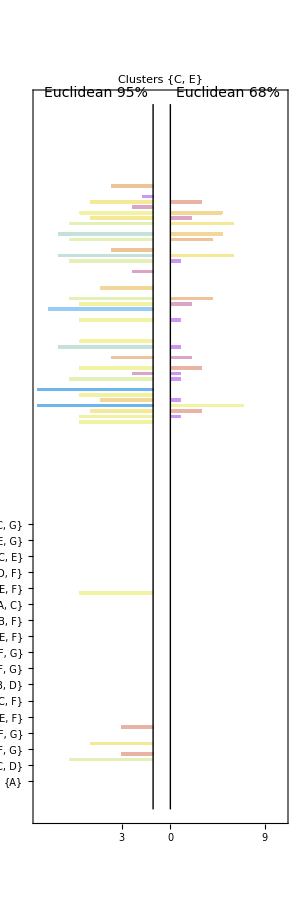
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
index=2;
CreatePairedBarChartsGrid[aLLcombinationsStatisticsEuclidean95[[index]],aLLcombinationsStatisticsEuclidean68[[index]],{"Euclidean 95%", "Euclidean 68%"},True]
```

## Final totals bar chart:

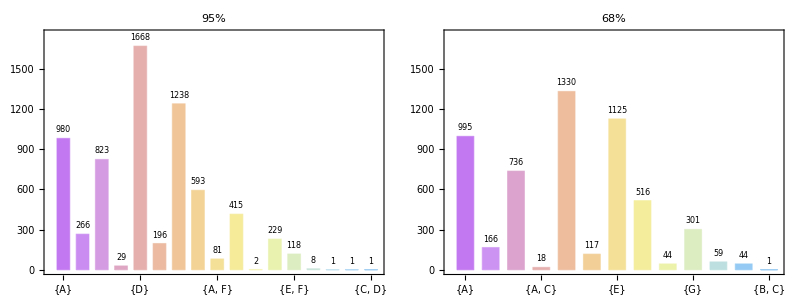

```mathematica
index=3;
eucl95=aLLcombinationsStatisticsEuclidean95[[index]];
eucl68=aLLcombinationsStatisticsEuclidean68[[index]];

joinedData={eucl95,eucl68};

stringList={"95%","68%"};

plotFinalBarCharts[joinedData,stringList,True]
```

```mathematica
Export["exportFinalGridCounts.pdf",exportFinalGridCounts]
```

exportFinalGridCounts.pdf

## Gerando Dataset de pontos dos dados:

```mathematica
aLLCOMBdataSetPointsEuclidean95=Dataset[allPointsToDataset[aLLCOMBeuclideanListOfClutersCombinationsResult95[[2]]]];
aLLCOMBdataSetPointsEuclidean95=transformedDataset[aLLCOMBdataSetPointsEuclidean95, aLLCOMBdataSetCombinationsEuclidean95];

aLLCOMBdataSetPointsEuclidean68=Dataset[allPointsToDataset[aLLCOMBeuclideanListOfClutersCombinationsResult68[[2]]]];
aLLCOMBdataSetPointsEuclidean68=transformedDataset[aLLCOMBdataSetPointsEuclidean68, aLLCOMBdataSetCombinationsEuclidean68];
```

## Checking RAM and exporting datasets:

```mathematica
Quiet[
symbolSizes=Table[{symbol,N[ByteCount[ToExpression[symbol]]/1024^2]},{symbol,Names["`*"]}];
    symbolSizes=SortBy[symbolSizes,Last]; (*Sort by size*)
top5Largest=Take[symbolSizes,-5];
   top5Largest//TableForm
]
```

aLLCOMBdataSetCombinationsEuclidean95Imported | 15.9552
aLLCOMBeuclideanListOfClutersCombinationsResult68 | 25.8869
aLLCOMBeuclideanListOfClutersCombinationsResult95 | 31.5494
aLLCOMBdataSetPointsEuclidean68 | 232.443
aLLCOMBdataSetPointsEuclidean95 | 283.547

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx2048m"]
```

LinkObject[…]

## Exportando os dataset de dados:

```mathematica
Export["aLLCOMBdataSetPointsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx", aLLCOMBdataSetPointsEuclidean95]

Export["aLLCOMBdataSetPointsEuclidean68_nSampling_"<>ToString[samplingsToRun]<>".xlsx", aLLCOMBdataSetPointsEuclidean68]
```

aLLCOMBdataSetPointsEuclidean95_nSampling_1.xlsx

aLLCOMBdataSetPointsEuclidean68_nSampling_1.xlsx

## Importando Datasets de dados:

```mathematica
aLLCOMBdataSetPointsEuclidean95Imported=Import["aLLCOMBdataSetPointsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetPointsEuclidean95Imported = aLLCOMBdataSetPointsEuclidean95Imported[All,{"Combination"->ToExpression,"parIndex"->Round,"SamplingIndex"->Round}];

aLLCOMBdataSetPointsEuclidean68Imported=Import["aLLCOMBdataSetPointsEuclidean68_nSampling_"<>ToString[samplingsToRun]<>".xlsx",{"Dataset",1},"HeaderLines"->1];
aLLCOMBdataSetPointsEuclidean68Imported = aLLCOMBdataSetPointsEuclidean68Imported[All,{"Combination"->ToExpression,"parIndex"->Round,"SamplingIndex"->Round}];
```

```mathematica
aLLCOMBdataSetPointsEuclidean95= aLLCOMBdataSetPointsEuclidean95Imported;

aLLCOMBdataSetPointsEuclidean68= aLLCOMBdataSetPointsEuclidean68Imported;
```

## Plot dos pontos de todos os parâmetros e elipsoides:

```mathematica
allPointsListAllCombs = {aLLCOMBdataSetPointsEuclidean95,aLLCOMBdataSetPointsEuclidean68};

(*filteredaLLCOMBdataSetPointsEuclidean95 = aLLCOMBdataSetPointsEuclidean95;
filteredaLLCOMBdataSetPointsEuclidean68 = aLLCOMBdataSetPointsEuclidean68;*)

{filteredaLLCOMBdataSetPointsEuclidean95, filteredaLLCOMBdataSetPointsEuclidean68} = Map[Normal[Values[#[Select[#parIndex==55 &],4;;]]]&,allPointsListAllCombs] ;
```

```mathematica
variablesToSelectCLusters={methodNBCdataclustTotal,methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightspercTotal};

summaryPlotEllipseAndPoints[filteredaLLCOMBdataSetPointsEuclidean95,{1,2,3,4,5,6,7},variablesToSelectCLusters,postotal,0.95,EuclideanDistance]

summaryPlotEllipseAndPoints[filteredaLLCOMBdataSetPointsEuclidean68,{1,2,3,4,5,6,7},variablesToSelectCLusters,postotal,0.68,EuclideanDistance]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

-Graphics3D- | -Graphics3D- | -Graphics3D-

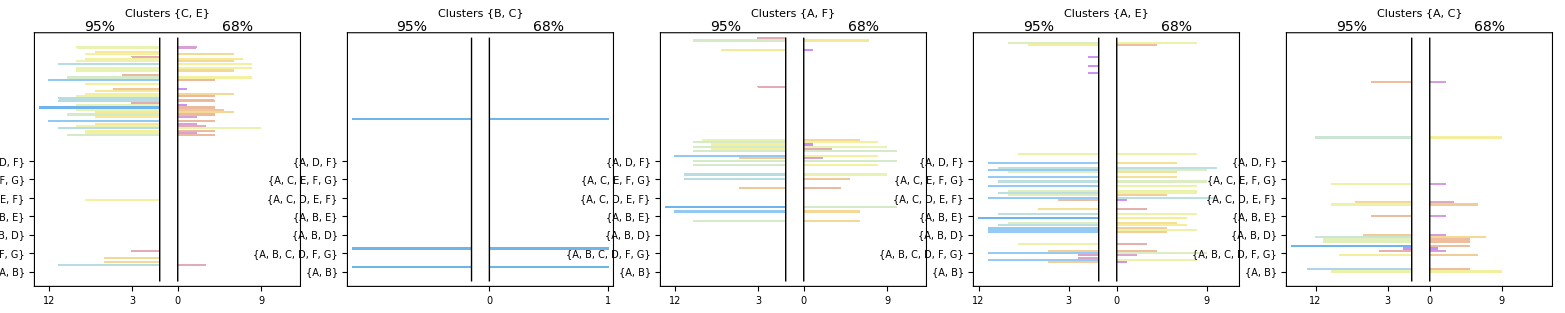

```mathematica
index=2;
listOfPairedBarChart2 = {7,9,11,12,13};
export2 = CreatePairedBarChartsGrid[editedPairedBarChartData2[[listOfPairedBarChart2]],refPairedBarChartData2[[listOfPairedBarChart2]],{"95%", "68%"},True,5]
```

```mathematica
Export["combsAllCombsEuclidean.pdf",export2]
```

combsAllCombs.pdf

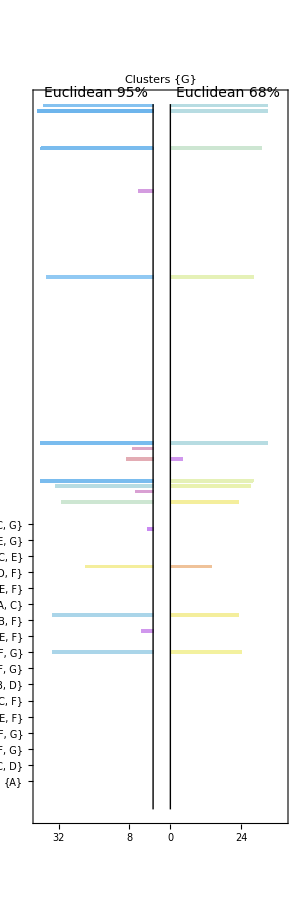
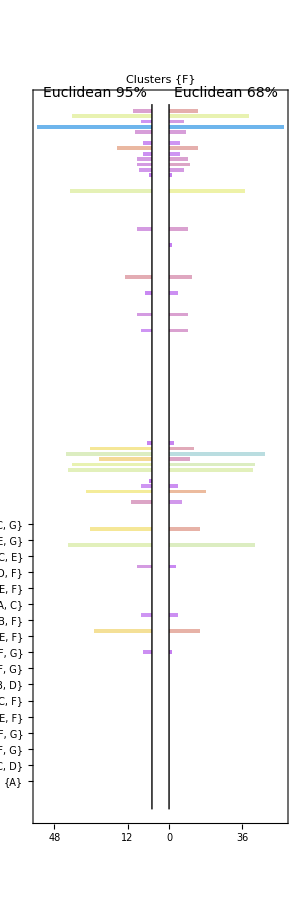
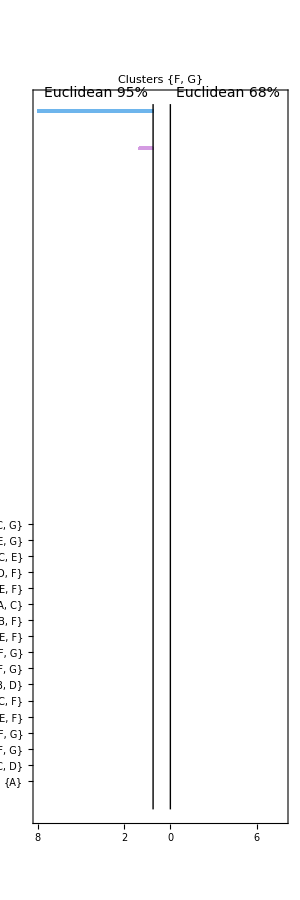
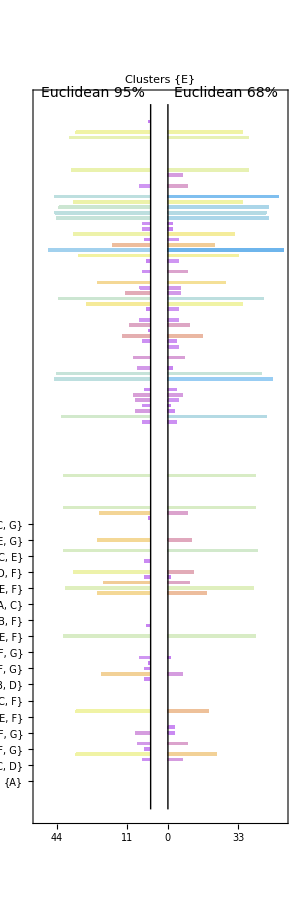
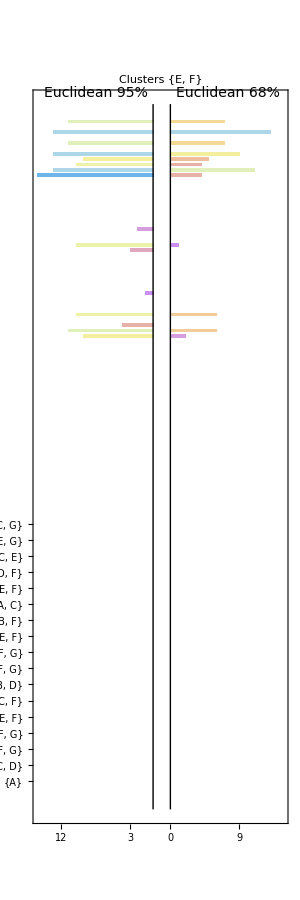
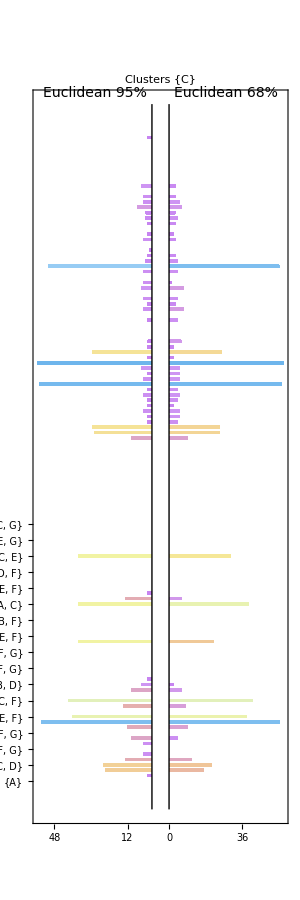
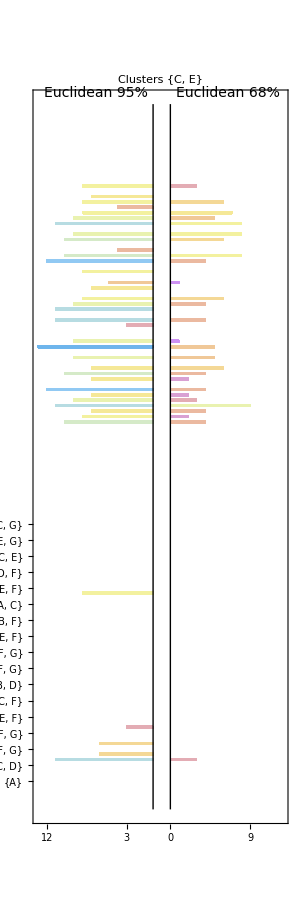
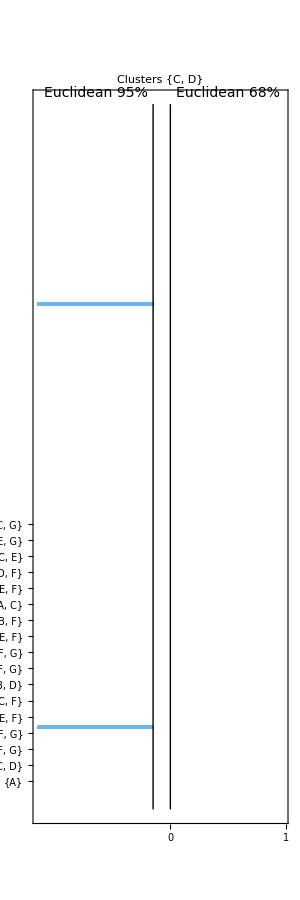
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
index=2;
CreatePairedBarChartsGrid[aLLcombinationsStatisticsEuclidean95[[index]],aLLcombinationsStatisticsEuclidean68[[index]],{"Euclidean 95%", "Euclidean 68%"},True]
```

# Parte 2.1-TODAS apenas euclidian 95% e mais samplings:

## Rodar análise:

```mathematica
(*-- carregador novamente os dados para garantir --*)
loadAllData[EuclideanDistance, postotal];
(*---------------------------------------------*)
```

```mathematica
(* cai de 56 parâmetros pra 25 e tirei 3 das quatro runs com mahnattan e percentuais *)
parSinputs = {0.5,4, 0.5};
parNinputs = {1,4, 0.5};
parsLimits={1/100, 10};

selectedNoiseFactor = 0.001;
selectedTimeForSimulation = 200;

samplingsToRun = 5;
uniformSampling = 5;
pertubationAmplitude = 1;
combinationsToTest=1;  (*  entra no modo de todas as combinações com 4 e 5*)

AbsoluteTiming[uniformALLCOMBeuclideanListOfClutersCombinationsResult95 = clustersCombinationsMoreThanTwo[methodNBCdataclustTotal,methodNBCdatabasinscentersTotal,methodNBCdatabasinssigmasTotal,methodNBCdataweightspercTotal,parSinputs,parNinputs,parsLimits,1,{1,2,3,4,5,6,7},samplingsToRun,uniformSampling,False,0.95,pertubationAmplitude,postotal,combinationsToTest, selectedNoiseFactor,selectedTimeForSimulation];]
Dimensions[aLLCOMBeuclideanListOfClutersCombinationsResult95]
```

Total number of clusters combinations: 127

{136625.,Null}

{3,127}

## Gerando Dataset:

```mathematica
uniformALLCOMBdataSetCombinationsEuclidean95=Dataset[generateCombinationsDataset[aLLCOMBeuclideanListOfClutersCombinationsResult95[[1]]]];
```

## Exportando Dataset:

```mathematica
Export["uniform_aLLCOMBdataSetCombinationsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx", uniformALLCOMBdataSetCombinationsEuclidean95]
```

uniform_aLLCOMBdataSetCombinationsEuclidean95_nSampling_5.xlsx

## Importando Datasets :

```mathematica
uniformALLCOMBdataSetCombinationsEuclidean95Imported=Import["uniform_aLLCOMBdataSetCombinationsEuclidean95_nSampling_"<>ToString[samplingsToRun]<>".xlsx",{"Dataset",1},"HeaderLines"->1];
uniformALLCOMBdataSetCombinationsEuclidean95Imported = uniformALLCOMBdataSetCombinationsEuclidean95Imported[All,{"Combination"->ToExpression,"ParIndex"->Round, "ClusterFilled"->ToExpression}];
```

```mathematica
uniformALLCOMBdataSetCombinationsEuclidean95= uniformALLCOMBdataSetCombinationsEuclidean95Imported;
```

## Clusters encontrados juntos e com quais frequências:

```mathematica
uniformALLcombinationsStatisticsEuclidean95= returnClustersCombinationsStatistics[uniformALLCOMBdataSetCombinationsEuclidean95, False];
```

## BarChart:

```mathematica
index=1;
CreateBarChartsGrid[uniformALLcombinationsStatisticsEuclidean95[[index]]]
(*Grid[{Map[CreateBarChartsGrid[#]&,{combinationsStatisticsEuclidean95One[[1]],combinationsStatisticsEuclidean68One[[1]],combinationsStatisticsManhattan95One[[1]],combinationsStatisticsManhattan68One[[1]]}]},Frame->False]*)
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
index=2;
CreateBarChartsGrid[uniformALLcombinationsStatisticsEuclidean95[[index]],True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

## Final totals bar chart:

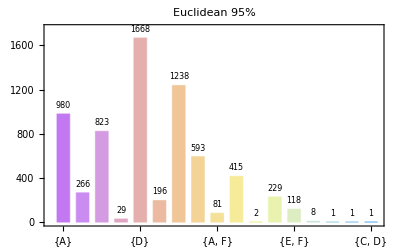

```mathematica
index=3;
eucl95=uniformALLcombinationsStatisticsEuclidean95[[index]];
joinedData={eucl95};

stringList={"Euclidean 95%"};

plotFinalBarCharts[joinedData,stringList,True]
```